# Getting of Numerical Results

For getting exact numerical data we will vary along μ but also get the data for the nS with different step value.

```mathematica
Clear["Global`*"]
```

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
Mvalues = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"];
```

```mathematica
μ = 90;
```

```mathematica
cini[4,μ]

cend[4,μ]
Mvalues[[μ,2]]
```

{79.69}

{89.3011}

0.00844129

### μ = 1

```mathematica
p= 4;
μ=1;
M :=0.0005167856394252862
ϕini =0.045514175860860345;
ϕend=0.659399152881071;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 4.054 10^8}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 4.054 10^8}, MaxStepSize->2000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,   10^8}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

InterpolatingFunction::dmval: Input value {1.1×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.2×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
tend
```

4.03329×10^8

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^7}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
r[0.002]
```

1.77746×10^-6

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00003}]]
```

{{0.00001,1.00118},{0.00004,0.943874},{0.00007,0.931941},{0.0001,0.939171},{0.00013,0.934084},{0.00016,0.941051},{0.00019,0.94239},{0.00022,0.936171},{0.00025,0.93701},{0.00028,0.939435},{0.00031,0.939337},{0.00034,0.938578},{0.00037,0.935229},{0.0004,0.939754},{0.00043,0.93791},{0.00046,0.935178},{0.00049,0.938794}}

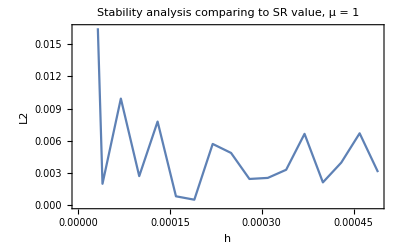

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9418793835059156)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 1 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
nS[0.002]
```

0.942074

```mathematica
{1,0.9420736577632982,1.7774602771495019*^-6}
```

{1,0.942074,1.77746×10^-6}

```mathematica
ld ={{0.00001,1.0011756000016943},{0.00004,0.9438737177706324},{0.00007000000000000001,0.9319410498809071},{0.0001,0.9391708153034904},{0.00013000000000000002,0.9340842391118719},{0.00016,0.9410514770870945},{0.00019,0.9423896456505468},{0.00022,0.9361706987519073},{0.00025,0.937009660401882},{0.00028000000000000003,0.9394350961303288},{0.00031000000000000005,0.9393370228305035},{0.00034,0.938578144479126},{0.00037000000000000005,0.9352293716180844},{0.0004,0.9397542921884025},{0.00043000000000000004,0.9379099234485465},{0.00046,0.9351781788821442},{0.00049,0.938794136134447}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.941828

0.0155852

### μ = 2

```mathematica
p= 4;
μ=2;
M :=0.001000827942960649
ϕini =0.1808718295733005;
ϕend=1.5413043716381905;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,1.081  10^8}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 1.081 10^8}, MaxStepSize->2000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,  1 10^8}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

InterpolatingFunction::dmval: Input value {1.2238×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.15007×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.11798×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
tend
```

1.07316×10^8

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^7}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00003}]]
```

{{0.00001,0.941533},{0.00004,0.943583},{0.00007,0.944152},{0.0001,0.944419},{0.00013,0.944578},{0.00016,0.943905},{0.00019,0.943209},{0.00022,0.94362},{0.00025,0.942443},{0.00028,0.943528},{0.00031,0.943313},{0.00034,0.94321},{0.00037,0.944076},{0.0004,0.943278},{0.00043,0.942709},{0.00046,0.942625},{0.00049,0.943023}}

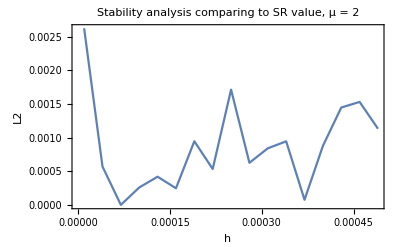

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9441561995712241)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 2 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{2,0.942994,0.0000252317}

```mathematica
ld = {{0.00001,0.9415329465607083},{0.00004,0.9435832386010365},{0.00007000000000000001,0.9441518368410734},{0.0001,0.9444185256905092},{0.00013000000000000002,0.9445784719040237},{0.00016,0.9439054548734089},{0.00019,0.9432085080389803},{0.00022,0.9436196474764169},{0.00025,0.9424432581520799},{0.00028000000000000003,0.9435278450763231},{0.00031000000000000005,0.9433129452997983},{0.00034,0.9432097775930782},{0.00037000000000000005,0.9440761542012992},{0.0004,0.9432776061290925},{0.00043000000000000004,0.942708712283604},{0.00046,0.9426251427789628},{0.00049,0.9430231405735103}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.943365

0.000770483

### μ = 3

```mathematica
p= 4;
μ=3;
M :=0.0014580208022664813
ϕini =0.402832179727929;
ϕend=2.4802703122079293;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,  5.1 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 5.1 10^7}, MaxStepSize->2000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,   5 10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

5.06054×10^7

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00003}]]
```

{{0.00001,0.953851},{0.00004,0.944116},{0.00007,0.938481},{0.0001,0.947388},{0.00013,0.943919},{0.00016,0.946975},{0.00019,0.947226},{0.00022,0.946404},{0.00025,0.946823},{0.00028,0.945926},{0.00031,0.946128},{0.00034,0.945885},{0.00037,0.945535},{0.0004,0.945904},{0.00043,0.945709},{0.00046,0.944663},{0.00049,0.946464}}

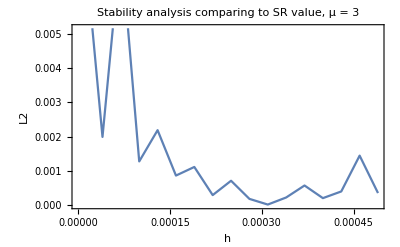

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9461098722369713)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 3 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{3,0.945783,0.000114648}

```mathematica
ld ={{0.00001,0.9538510349111217},{0.00004,0.9441158822310617},{0.00007000000000000001,0.9384811365599968},{0.0001,0.9473884627495907},{0.00013000000000000002,0.9439187599251668},{0.00016,0.9469749445233578},{0.00019,0.9472262756327825},{0.00022,0.9464043271282064},{0.00025,0.9468233238138434},{0.00028000000000000003,0.9459262487933309},{0.00031000000000000005,0.9461279487338994},{0.00034,0.9458851209694397},{0.00037000000000000005,0.9455351202162146},{0.0004,0.9459040339912693},{0.00043000000000000004,0.9457088349888567},{0.00046,0.9446625507826952},{0.00049,0.9464642245938292}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.945965

0.00288969

### μ = 4

```mathematica
p= 4;
μ=4;
M :=0.0018850574173281628
ϕini =0.7064516737152218;
ϕend=3.443139654313993;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,  3.04 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 3.04 10^7}, MaxStepSize->2000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,   3.03 10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.03668×10^7

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.881274},{0.00002,0.911858},{0.00003,0.935955},{0.00004,0.935037},{0.00005,0.951669},{0.00006,0.952237},{0.00007,0.949988},{0.00008,0.955024},{0.00009,0.950982},{0.0001,0.949523},{0.00011,0.945679},{0.00012,0.948043},{0.00013,0.941753},{0.00014,0.945951},{0.00015,0.947189},{0.00016,0.949051},{0.00017,0.94933},{0.00018,0.948192},{0.00019,0.9479},{0.0002,0.949094},{0.00021,0.94648},{0.00022,0.947688},{0.00023,0.945844},{0.00024,0.946542},{0.00025,0.945831},{0.00026,0.94533},{0.00027,0.948658},{0.00028,0.947414},{0.00029,0.948108},{0.0003,0.94662},{0.00031,0.947148},{0.00032,0.946705},{0.00033,0.948372},{0.00034,0.949428},{0.00035,0.946141},{0.00036,0.946643},{0.00037,0.948738},{0.00038,0.948625},{0.00039,0.946967},{0.0004,0.946609},{0.00041,0.946534},{0.00042,0.947802},{0.00043,0.948641},{0.00044,0.947627},{0.00045,0.947784},{0.00046,0.94766},{0.00047,0.947048},{0.00048,0.948802},{0.00049,0.94798},{0.0005,0.947072}}

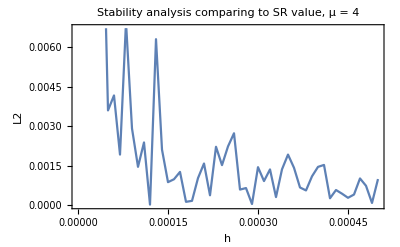

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9480646003630375)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 4 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{4,0.947189,0.000322908}

```mathematica
ld = {{0.000030000000000000004,0.9359553587282772},{0.00004,0.9350370254470688},{0.00005,0.951668633294004},{0.00006,0.9522374986210438},{0.00007000000000000001,0.9499881542836891},{0.00008,0.9550240535205503},{0.00009,0.9509815630922498},{0.0001,0.9495232488150529},{0.00011,0.9456794794571787},{0.00012,0.9480426719218202},{0.00013000000000000002,0.9417527612883648},{0.00014000000000000001,0.9459512577324005},{0.00015000000000000001,0.9471891676435628},{0.00016,0.9490507447374422},{0.00017,0.9493296936286215},{0.00018,0.9481920066614586},{0.00019,0.9479003810962916},{0.0002,0.9490935646508568},{0.00021,0.94648015914393},{0.00022,0.9476883100860005},{0.00023,0.9458436842775544},{0.00024,0.9465419907383401},{0.00025,0.9458310746938656},{0.00026000000000000003,0.9453302128189183},{0.00027000000000000006,0.9486577353646944},{0.0002800000000000001,0.9474136444916741},{0.00029000000000000006,0.9481084241506074},{0.00030000000000000003,0.9466195473550096},{0.00031000000000000005,0.9471480084513592},{0.00032,0.9467049102790109},{0.00033000000000000005,0.9483718001982511},{0.0003400000000000001,0.9494279160363909},{0.00035000000000000005,0.9461408968276867},{0.0003600000000000001,0.9466429782144091},{0.0003700000000000001,0.9487377512324721},{0.0003800000000000001,0.9486254563791671},{0.00039000000000000005,0.9469672797117205},{0.0004000000000000001,0.9466085360834129},{0.00041000000000000005,0.9465343745279643},{0.00042000000000000007,0.9478017022773342},{0.0004300000000000001,0.9486407266949463},{0.00044000000000000007,0.9476273022991555},{0.00045000000000000004,0.9477838242012668},{0.00046000000000000007,0.9476600627841356},{0.00047000000000000004,0.9470482208237937},{0.00048000000000000007,0.9488022529213078},{0.0004900000000000001,0.9479802758651306},{0.0005000000000000001,0.9470719376574794}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.947363

0.00321495

### μ = 5

```mathematica
p= 4;
μ=5;
M :=0.0022795949240379887
ϕini =1.0855624435544302;
ϕend=4.4182225131595;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,   2.1  10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 2.1  10^7}, MaxStepSize->2000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,    2.07 10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

2.08678×10^7

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.863816},{0.00002,0.971155},{0.00003,0.94017},{0.00004,0.948355},{0.00005,0.94736},{0.00006,0.951679},{0.00007,0.954953},{0.00008,0.947755},{0.00009,0.948085},{0.0001,0.95682},{0.00011,0.951794},{0.00012,0.955021},{0.00013,0.948993},{0.00014,0.949069},{0.00015,0.944806},{0.00016,0.94901},{0.00017,0.950008},{0.00018,0.948638},{0.00019,0.950799},{0.0002,0.946465},{0.00021,0.94717},{0.00022,0.949132},{0.00023,0.951801},{0.00024,0.949504},{0.00025,0.945789},{0.00026,0.952884},{0.00027,0.950837},{0.00028,0.951732},{0.00029,0.949956},{0.0003,0.948516},{0.00031,0.949596},{0.00032,0.947517},{0.00033,0.949683},{0.00034,0.948737},{0.00035,0.951398},{0.00036,0.949683},{0.00037,0.949849},{0.00038,0.950694},{0.00039,0.949996},{0.0004,0.952092},{0.00041,0.950429},{0.00042,0.94995},{0.00043,0.948413},{0.00044,0.948667},{0.00045,0.950102},{0.00046,0.948991},{0.00047,0.94884},{0.00048,0.948847},{0.00049,0.949074},{0.0005,0.947815}}

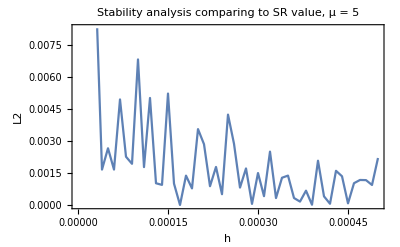

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9500166979192515)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 5 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{5,0.947372,0.000694726}

```mathematica
ld = {{0.00001,0.8638159742171456},{0.00002,0.9711546496175357},{0.000030000000000000004,0.9401701550482834},{0.00004,0.9483547516618619},{0.00005,0.9473603698083763},{0.00006,0.9516790131859517},{0.00007000000000000001,0.9549526921848405},{0.00008,0.9477547866456741},{0.00009,0.9480852406580927},{0.0001,0.9568199924631277},{0.00011,0.951793981327177},{0.00012,0.9550210145259653},{0.00013000000000000002,0.9489934358134579},{0.00014000000000000001,0.9490693702251768},{0.00015000000000000001,0.9448059469281507},{0.00016,0.949010193890261},{0.00017,0.9500077378811775},{0.00018,0.9486379106022403},{0.00019,0.9507993686076603},{0.0002,0.946465452307276},{0.00021,0.9471701406362815},{0.00022,0.9491320230880579},{0.00023,0.9518013441526524},{0.00024,0.9495042142447503},{0.00025,0.9457894959192745},{0.00026000000000000003,0.9528835902633808},{0.00027000000000000006,0.9508370692842385},{0.0002800000000000001,0.951731871612196},{0.00029000000000000006,0.9499563312248659},{0.00030000000000000003,0.9485158501453076},{0.00031000000000000005,0.9495961702230252},{0.00032,0.9475173528182064},{0.00033000000000000005,0.9496834874043678},{0.0003400000000000001,0.9487366853366493},{0.00035000000000000005,0.951397682302173},{0.0003600000000000001,0.9496827700246534},{0.0003700000000000001,0.9498494908115149},{0.0003800000000000001,0.9506939048312476},{0.00039000000000000005,0.9499957758565468},{0.0004000000000000001,0.9520920799934052},{0.00041000000000000005,0.9504292655705511},{0.00042000000000000007,0.9499500733330138},{0.0004300000000000001,0.9484126229410987},{0.00044000000000000007,0.948667058002773},{0.00045000000000000004,0.950102101880796},{0.00046000000000000007,0.9489906633961575},{0.00047000000000000004,0.9488402652207599},{0.00048000000000000007,0.9488474371693534},{0.0004900000000000001,0.9490738871987731},{0.0005000000000000001,0.9478149017574998}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.948249

0.012823

### μ = 6

```mathematica
p= 4;
μ=6;
M :=0.0026409781815723244
ϕini =1.5333018469110486;
ϕend=5.4003635322549215;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 1.57    10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,1.57  10^7}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,    1.57  10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

1.56489×10^7

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00003}]]
```

{{0.00001,0.943037},{0.00004,0.952623},{0.00007,0.950227},{0.0001,0.954154},{0.00013,0.952517},{0.00016,0.951718},{0.00019,0.953557},{0.00022,0.953779},{0.00025,0.951731},{0.00028,0.952342},{0.00031,0.9526},{0.00034,0.951925},{0.00037,0.951395},{0.0004,0.951495},{0.00043,0.95141},{0.00046,0.950943},{0.00049,0.951069}}

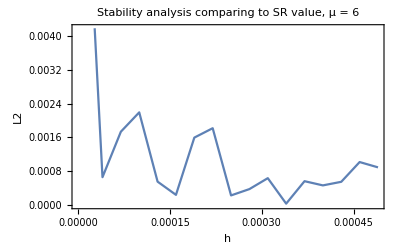

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9519617881755984)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 6 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{6,0.951957,0.00126059}

```mathematica
ld = {{0.00001,0.9430370983279321},{0.00004,0.952622619092677},{0.00007000000000000001,0.9502270776964371},{0.0001,0.9541535004490553},{0.00013000000000000002,0.952517253696942},{0.00016,0.9517180445773563},{0.00019,0.9535572739624495},{0.00022,0.9537792203873775},{0.00025,0.9517312963956627},{0.00028000000000000003,0.9523417258630661},{0.00031000000000000005,0.9525995321290893},{0.00034,0.9519254118712953},{0.00037000000000000005,0.9513952725603259},{0.0004,0.9514945927642098},{0.00043000000000000004,0.9514100221773251},{0.00046,0.9509434166984122},{0.00049,0.9510690340695057}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.95156

0.0024323

### μ = 7

```mathematica
p= 4;
μ=7;
M :=0.0029700341589078984
ϕini =2.0425907641201966;
ϕend=6.386944020293249;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,1.25 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  1.25 10^7}, MaxStepSize->5000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,    1.25  10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

1.24703×10^7

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
hc[0.002]//N
```

1.17832×10^6

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.995479},{0.00002,0.959041},{0.00003,0.959467},{0.00004,0.950106},{0.00005,0.955748},{0.00006,0.959081},{0.00007,0.95824},{0.00008,0.953106},{0.00009,0.953776},{0.0001,0.958061},{0.00011,0.952785},{0.00012,0.952971},{0.00013,0.954234},{0.00014,0.953176},{0.00015,0.954373},{0.00016,0.956131},{0.00017,0.954654},{0.00018,0.955736},{0.00019,0.955505},{0.0002,0.954448},{0.00021,0.952697},{0.00022,0.953761},{0.00023,0.954261},{0.00024,0.954353},{0.00025,0.954847},{0.00026,0.952818},{0.00027,0.954493},{0.00028,0.953583},{0.00029,0.953822},{0.0003,0.953824},{0.00031,0.953656},{0.00032,0.953513},{0.00033,0.954683},{0.00034,0.9542},{0.00035,0.95375},{0.00036,0.953259},{0.00037,0.954545},{0.00038,0.954735},{0.00039,0.953145},{0.0004,0.952902},{0.00041,0.953078},{0.00042,0.954206},{0.00043,0.954045},{0.00044,0.954071},{0.00045,0.95404},{0.00046,0.953924},{0.00047,0.952928},{0.00048,0.953175},{0.00049,0.953679},{0.0005,0.95331}}

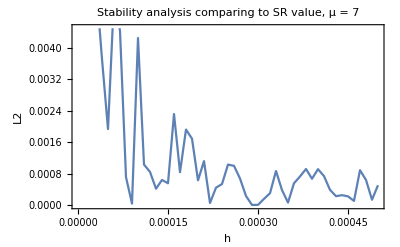

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9538161652033381)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 7 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{7,0.954373,0.00202665}

```mathematica
ld = {{0.00002,0.9590411589693476},{0.000030000000000000004,0.9594667768060049},{0.00004,0.9501059105254297},{0.00005,0.9557477646611404},{0.00006,0.9590807725932239},{0.00007000000000000001,0.9582403547750984},{0.00008,0.9531056069791579},{0.00009,0.9537761558712937},{0.0001,0.9580610820425749},{0.00011,0.9527853498900474},{0.00012,0.9529711024097078},{0.00013000000000000002,0.9542341365264072},{0.00014000000000000001,0.953175871722515},{0.00015000000000000001,0.9543732058140167},{0.00016,0.9561309628882376},{0.00017,0.954653931040137},{0.00018,0.9557362434996213},{0.00019,0.955505477081524},{0.0002,0.9544478730920927},{0.00021,0.952697282872158},{0.00022,0.9537609965759529},{0.00023,0.9542610813331991},{0.00024,0.9543525338212582},{0.00025,0.9548471439735516},{0.00026000000000000003,0.9528178707406934},{0.00027000000000000006,0.9544929583461016},{0.0002800000000000001,0.953583252073004},{0.00029000000000000006,0.9538224763111416},{0.00030000000000000003,0.9538244153688273},{0.00031000000000000005,0.9536559769938622},{0.00032,0.9535126086961486},{0.00033000000000000005,0.9546834267951411},{0.0003400000000000001,0.9541999036629193},{0.00035000000000000005,0.953750297409076},{0.0003600000000000001,0.9532589883101392},{0.0003700000000000001,0.9545448493831978},{0.0003800000000000001,0.9547354156893674},{0.00039000000000000005,0.9531454015854472},{0.0004000000000000001,0.9529015169729171},{0.00041000000000000005,0.9530780332579074},{0.00042000000000000007,0.95420550932456},{0.0004300000000000001,0.9540446770395494},{0.00044000000000000007,0.9540705380238027},{0.00045000000000000004,0.9540402890010875},{0.00046000000000000007,0.9539241168772312},{0.00047000000000000004,0.9529277521611471},{0.00048000000000000007,0.9531750368620263},{0.0004900000000000001,0.9536785597056026},{0.0005000000000000001,0.9533104623593855}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.954366

0.00179146

### μ = 8

```mathematica
p= 4;
μ=8;
M :=0.003268644560167123
ϕini =2.606507629570049;
ϕend=7.376495437761909;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,1.05 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 1.05  10^7}, MaxStepSize->300,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,    1.05  10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

1.03874×10^7

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00003}]]
```

{{0.00001,0.975638},{0.00004,0.957528},{0.00007,0.956725},{0.0001,0.953508},{0.00013,0.954448},{0.00016,0.955583},{0.00019,0.956487},{0.00022,0.957561},{0.00025,0.95587},{0.00028,0.955885},{0.00031,0.95495},{0.00034,0.955332},{0.00037,0.95529},{0.0004,0.955419},{0.00043,0.954699},{0.00046,0.955185},{0.00049,0.954975}}

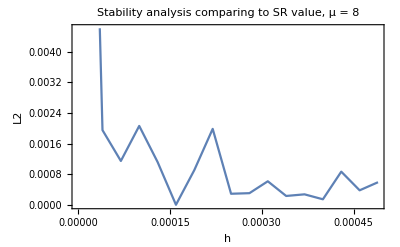

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9555724963149217)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 8 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{8,0.954999,0.00298272}

```mathematica
ld = {{0.00004,0.9575278291188732},{0.00007000000000000001,0.9567246520121754},{0.0001,0.9535078502584021},{0.00013000000000000002,0.9544479082845067},{0.00016,0.9555828181591113},{0.00019,0.956487088673271},{0.00022,0.9575606281645552},{0.00025,0.9558700989308653},{0.00028000000000000003,0.9558852209231088},{0.00031000000000000005,0.9549499721384919},{0.00034,0.9553323559127255},{0.00037000000000000005,0.9552900685691088},{0.0004,0.9554191326756429},{0.00043000000000000004,0.9546992039251312},{0.00046,0.9551852168834318},{0.00049,0.9549746124779078}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.95559

0.00107912

### μ = 9

```mathematica
p= 4;
μ=9;
M :=0.003539295399199606
ϕini =3.218543646875904;
ϕend=8.3681314518296;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,9 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  9 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      9 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

8.94581×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.97914},{0.00002,0.91936},{0.00003,0.958786},{0.00004,0.949284},{0.00005,0.958327},{0.00006,0.952194},{0.00007,0.954872},{0.00008,0.955799},{0.00009,0.959997},{0.0001,0.957672},{0.00011,0.957606},{0.00012,0.958035},{0.00013,0.954496},{0.00014,0.959143},{0.00015,0.956094},{0.00016,0.960212},{0.00017,0.958703},{0.00018,0.957075},{0.00019,0.957887},{0.0002,0.957554},{0.00021,0.959877},{0.00022,0.957122},{0.00023,0.958145},{0.00024,0.956245},{0.00025,0.956739},{0.00026,0.956436},{0.00027,0.957624},{0.00028,0.956597},{0.00029,0.957398},{0.0003,0.958307},{0.00031,0.958573},{0.00032,0.957825},{0.00033,0.957641},{0.00034,0.955588},{0.00035,0.958023},{0.00036,0.955013},{0.00037,0.957273},{0.00038,0.956911},{0.00039,0.956505},{0.0004,0.956279},{0.00041,0.956938},{0.00042,0.956821},{0.00043,0.95624},{0.00044,0.957337},{0.00045,0.957079},{0.00046,0.956897},{0.00047,0.956849},{0.00048,0.956956},{0.00049,0.956385},{0.0005,0.956945}}

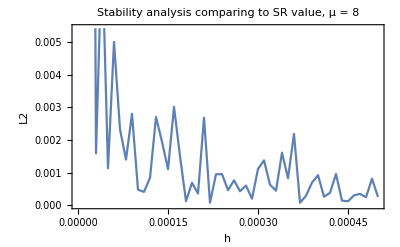

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9571976671275582)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 8 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{9,0.956094,0.00410689}

```mathematica
ld= {{0.000030000000000000004,0.9587861077381085},{0.00004,0.9492842111740063},{0.00005,0.9583266515233075},{0.00006,0.9521938796277556},{0.00007000000000000001,0.9548717045496969},{0.00008,0.9557991833825663},{0.00009,0.9599970916499646},{0.0001,0.957672196872677},{0.00011,0.957606079080815},{0.00012,0.9580345944835007},{0.00013000000000000002,0.9544956045238125},{0.00014000000000000001,0.959143341370849},{0.00015000000000000001,0.9560938816464495},{0.00016,0.960212189602464},{0.00017,0.9587032634779861},{0.00018,0.9570753309357231},{0.00019,0.9578866006026963},{0.0002,0.9575541563240202},{0.00021,0.9598772180269711},{0.00022,0.9571221552007256},{0.00023,0.958144849135696},{0.00024,0.9562449084445827},{0.00025,0.9567389293525661},{0.00026000000000000003,0.956436067724437},{0.00027000000000000006,0.9576239028391235},{0.0002800000000000001,0.9565971234563159},{0.00029000000000000006,0.9573980117192397},{0.00030000000000000003,0.9583068914662383},{0.00031000000000000005,0.9585728952917254},{0.00032,0.9578250775429653},{0.00033000000000000005,0.95764142062959},{0.0003400000000000001,0.955588248995431},{0.00035000000000000005,0.958023062262025},{0.0003600000000000001,0.9550126430748458},{0.0003700000000000001,0.9572731833107988},{0.0003800000000000001,0.9569113787639383},{0.00039000000000000005,0.956505108830033},{0.0004000000000000001,0.9562786123153804},{0.00041000000000000005,0.9569376008462471},{0.00042000000000000007,0.9568209491687504},{0.0004300000000000001,0.9562404897790768},{0.00044000000000000007,0.9573367758009429},{0.00045000000000000004,0.9570786490122176},{0.00046000000000000007,0.9568967344596314},{0.00047000000000000004,0.956848946848122},{0.00048000000000000007,0.9569558291870117},{0.0004900000000000001,0.9563854576649485},{0.0005000000000000001,0.9569449331357133}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.957006

0.00182162

### μ = 10

```mathematica
p= 4;
μ=10;
M :=0.0037847341996481098
ϕini =3.872750413269875;
ϕend=9.361285850366938;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,7.95 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  7.95 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      7.95 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

7.90462×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.968827},{0.00002,0.963764},{0.00003,0.961368},{0.00004,0.959405},{0.00005,0.956985},{0.00006,0.960292},{0.00007,0.95991},{0.00008,0.956686},{0.00009,0.957108},{0.0001,0.958842},{0.00011,0.960486},{0.00012,0.96057},{0.00013,0.959738},{0.00014,0.959844},{0.00015,0.959068},{0.00016,0.959339},{0.00017,0.96},{0.00018,0.959254},{0.00019,0.958822},{0.0002,0.959355},{0.00021,0.958673},{0.00022,0.958503},{0.00023,0.959237},{0.00024,0.959707},{0.00025,0.958756},{0.00026,0.959253},{0.00027,0.958354},{0.00028,0.958585},{0.00029,0.958878},{0.0003,0.958363},{0.00031,0.958854},{0.00032,0.958709},{0.00033,0.958785},{0.00034,0.959139},{0.00035,0.958773},{0.00036,0.958344},{0.00037,0.958094},{0.00038,0.95873},{0.00039,0.958072},{0.0004,0.95824},{0.00041,0.958924},{0.00042,0.958915},{0.00043,0.958663},{0.00044,0.958348},{0.00045,0.958795},{0.00046,0.958112},{0.00047,0.958269},{0.00048,0.957935},{0.00049,0.957942},{0.0005,0.957855}}

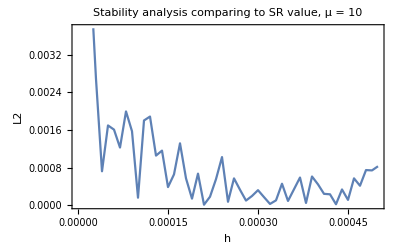

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9586827591108323)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 10 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{10,0.959068,0.0053673}

```mathematica
0.9586827591108323
```

```mathematica
ld = {{0.00001,0.9688273937660322},{0.00002,0.963763698439379},{0.000030000000000000004,0.9613683392993058},{0.00004,0.9594046317852021},{0.00005,0.9569849018821686},{0.00006,0.9602917291263161},{0.00007000000000000001,0.9599096372980389},{0.00008,0.9566863371996301},{0.00009,0.9571082011855805},{0.0001,0.9588419661008296},{0.00011,0.9604863210029363},{0.00012,0.9605697481079337},{0.00013000000000000002,0.9597384695743134},{0.00014000000000000001,0.9598443223051412},{0.00015000000000000001,0.9590680463234112},{0.00016,0.9593385625267141},{0.00017,0.9599995808915075},{0.00018,0.9592538578990462},{0.00019,0.9588218714660979},{0.0002,0.9593545845204363},{0.00021,0.9586729616331194},{0.00022,0.9585031219747837},{0.00023,0.9592370288535967},{0.00024,0.9597066032156626},{0.00025,0.9587555335723743},{0.00026000000000000003,0.9592530235626548},{0.00027000000000000006,0.9583542802261795},{0.0002800000000000001,0.958584624405618},{0.00029000000000000006,0.9588783214984179},{0.00030000000000000003,0.9583632840057833},{0.00031000000000000005,0.9588542586234321},{0.00032,0.9587091065201453},{0.00033000000000000005,0.958785387134507},{0.0003400000000000001,0.9591392173616743},{0.00035000000000000005,0.9587729038227301},{0.0003600000000000001,0.9583436958578505},{0.0003700000000000001,0.9580941140697176},{0.0003800000000000001,0.9587296379933742},{0.00039000000000000005,0.9580722023834685},{0.0004000000000000001,0.9582395069246336},{0.00041000000000000005,0.9589243086517486},{0.00042000000000000007,0.9589145289674509},{0.0004300000000000001,0.9586629531700217},{0.00044000000000000007,0.9583479316917968},{0.00045000000000000004,0.9587953381646406},{0.00046000000000000007,0.9581117427982393},{0.00047000000000000004,0.9582688064274338},{0.00048000000000000007,0.9579353888529537},{0.0004900000000000001,0.9579422545171172},{0.0005000000000000001,0.957854592673354}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.959149

0.00179127

### μ = 11

```mathematica
p= 4;
μ=11;
M :=0.004007715174296988
ϕini =4.563803387444165;
ϕend=10.35558017238564;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,7.27 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  7.27 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      7.2 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

7.12653×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.964149},{0.00002,0.945368},{0.00003,0.963838},{0.00004,0.960338},{0.00005,0.961275},{0.00006,0.95857},{0.00007,0.963155},{0.00008,0.958953},{0.00009,0.959903},{0.0001,0.960734},{0.00011,0.961372},{0.00012,0.960286},{0.00013,0.961385},{0.00014,0.959337},{0.00015,0.959862},{0.00016,0.96059},{0.00017,0.959219},{0.00018,0.960194},{0.00019,0.959834},{0.0002,0.961082},{0.00021,0.960232},{0.00022,0.960053},{0.00023,0.961112},{0.00024,0.960224},{0.00025,0.960743},{0.00026,0.959892},{0.00027,0.960399},{0.00028,0.959464},{0.00029,0.960515},{0.0003,0.959815},{0.00031,0.960126},{0.00032,0.959733},{0.00033,0.959367},{0.00034,0.960627},{0.00035,0.960618},{0.00036,0.959738},{0.00037,0.95961},{0.00038,0.959643},{0.00039,0.960569},{0.0004,0.959672},{0.00041,0.959657},{0.00042,0.96048},{0.00043,0.960322},{0.00044,0.959248},{0.00045,0.9595},{0.00046,0.95937},{0.00047,0.959976},{0.00048,0.959994},{0.00049,0.95967},{0.0005,0.959596}}

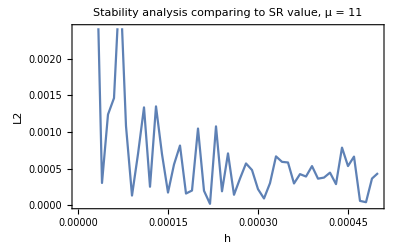

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9600345070570707)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 11 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{11,0.959862,0.00673238}

```mathematica
ld = {{0.00001,0.9641486742752527},{0.00002,0.9453675290398128},{0.000030000000000000004,0.9638383801443177},{0.00004,0.9603382704945586},{0.00005,0.9612745118804299},{0.00006,0.9585703466268088},{0.00007000000000000001,0.9631547695114236},{0.00008,0.9589529507085701},{0.00009,0.9599030360877201},{0.0001,0.9607340765373612},{0.00011,0.9613716433105864},{0.00012,0.960286499920018},{0.00013000000000000002,0.9613853885226875},{0.00014000000000000001,0.9593371084578062},{0.00015000000000000001,0.9598617874564745},{0.00016,0.9605904000661067},{0.00017,0.9592190001574125},{0.00018,0.960193686583655},{0.00019,0.9598341997813388},{0.0002,0.9610824654464023},{0.00021,0.9602315222744419},{0.00022,0.9600528137349382},{0.00023,0.9611120762140183},{0.00024,0.9602243485632697},{0.00025,0.9607425203378036},{0.00026000000000000003,0.9598924309676139},{0.00027000000000000006,0.9603985217763721},{0.0002800000000000001,0.9594641170837545},{0.00029000000000000006,0.9605152452886434},{0.00030000000000000003,0.9598152764500217},{0.00031000000000000005,0.960126174531236},{0.00032,0.9597334362458816},{0.00033000000000000005,0.9593672874191975},{0.0003400000000000001,0.9606267038733403},{0.00035000000000000005,0.9606183568143867},{0.0003600000000000001,0.9597376791316761},{0.0003700000000000001,0.9596099807264837},{0.0003800000000000001,0.9596427088190234},{0.00039000000000000005,0.9605688197458586},{0.0004000000000000001,0.9596720619364413},{0.00041000000000000005,0.9596572312428976},{0.00042000000000000007,0.9604795068458754},{0.0004300000000000001,0.9603222775813473},{0.00044000000000000007,0.9592476270699197},{0.00045000000000000004,0.9594999474827938},{0.00046000000000000007,0.959370477780608},{0.00047000000000000004,0.9599759068607201},{0.00048000000000000007,0.9599938519206942},{0.0004900000000000001,0.9596703383096086},{0.0005000000000000001,0.9595958629547005}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;2]]]
```

0.959988

{7.07107×10^-6,0.0132803}

### μ = 12

```mathematica
p= 4;
μ=12;
M :=0.004210852044236141
ϕini =5.287006747078254;
ϕend=11.35075193327038;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,6.55 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  6.55 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      6.55 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

6.52856×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.998599},{0.00002,0.954306},{0.00003,0.957855},{0.00004,0.943649},{0.00005,0.972341},{0.00006,0.964275},{0.00007,0.963282},{0.00008,0.961154},{0.00009,0.96188},{0.0001,0.962211},{0.00011,0.963256},{0.00012,0.962166},{0.00013,0.958924},{0.00014,0.960609},{0.00015,0.961211},{0.00016,0.961515},{0.00017,0.961555},{0.00018,0.961086},{0.00019,0.961047},{0.0002,0.96139},{0.00021,0.961657},{0.00022,0.96186},{0.00023,0.961634},{0.00024,0.961477},{0.00025,0.960825},{0.00026,0.9624},{0.00027,0.96243},{0.00028,0.96125},{0.00029,0.961193},{0.0003,0.961164},{0.00031,0.962232},{0.00032,0.961512},{0.00033,0.961322},{0.00034,0.960115},{0.00035,0.961617},{0.00036,0.960669},{0.00037,0.960498},{0.00038,0.960406},{0.00039,0.960965},{0.0004,0.961173},{0.00041,0.961626},{0.00042,0.96082},{0.00043,0.961755},{0.00044,0.961583},{0.00045,0.960635},{0.00046,0.960738},{0.00047,0.961497},{0.00048,0.960804},{0.00049,0.960475},{0.0005,0.960785}}

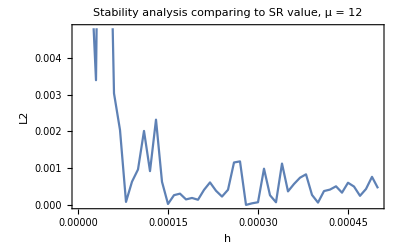

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9612430892601784)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 12 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{12,0.961211,0.00817853}

```mathematica
ld = {{0.00002,0.9543061634130531},{0.000030000000000000004,0.9578545111882122},{0.00004,0.943649421231469},{0.00005,0.9723408239888263},{0.00006,0.9642754137975901},{0.00007000000000000001,0.9632822796453689},{0.00008,0.9611536763425622},{0.00009,0.9618803078946404},{0.0001,0.96221103625353},{0.00011,0.9632559148356975},{0.00012,0.9621660718887531},{0.00013000000000000002,0.9589244403069626},{0.00014000000000000001,0.9606092937491377},{0.00015000000000000001,0.9612106127037979},{0.00016,0.9615145273771097},{0.00017,0.9615552809075241},{0.00018,0.9610863889127602},{0.00019,0.9610474746412074},{0.0002,0.961390455235265},{0.00021,0.9616572064141481},{0.00022,0.9618599324547781},{0.00023,0.9616339502162895},{0.00024,0.9614767533091041},{0.00025,0.9608253397912935},{0.00026000000000000003,0.962400455695695},{0.00027000000000000006,0.9624304079018207},{0.0002800000000000001,0.9612504525202206},{0.00029000000000000006,0.9611931078255993},{0.00030000000000000003,0.9611635693481233},{0.00031000000000000005,0.9622315527762977},{0.00032,0.961512172102156},{0.00033000000000000005,0.961322087475257},{0.0003400000000000001,0.9601154904750661},{0.00035000000000000005,0.9616170061173688},{0.0003600000000000001,0.9606689028365742},{0.0003700000000000001,0.9604984667261828},{0.0003800000000000001,0.9604063608380121},{0.00039000000000000005,0.9609650125646539},{0.0004000000000000001,0.96117290143713},{0.00041000000000000005,0.9616257882698122},{0.00042000000000000007,0.9608204219655238},{0.0004300000000000001,0.9617545561240609},{0.00044000000000000007,0.9615825596119334},{0.00045000000000000004,0.9606348122053803},{0.00046000000000000007,0.9607378051968165},{0.00047000000000000004,0.9614967540146651},{0.00048000000000000007,0.9608040910461849},{0.0004900000000000001,0.9604749432450711},{0.0005000000000000001,0.9607851339114456}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.961037

0.00331059

### μ = 13

```mathematica
p= 4;
μ=13;
M :=0.004396538698533752
ϕini =6.038261766959208;
ϕend=12.34661340606405;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,6.1 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  6.1 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      6 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

6.05813×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.943842},{0.00002,0.953549},{0.00003,0.961595},{0.00004,0.962309},{0.00005,0.960642},{0.00006,0.96371},{0.00007,0.961645},{0.00008,0.958096},{0.00009,0.963716},{0.0001,0.959188},{0.00011,0.964068},{0.00012,0.964694},{0.00013,0.965552},{0.00014,0.961344},{0.00015,0.962291},{0.00016,0.961969},{0.00017,0.962241},{0.00018,0.962181},{0.00019,0.96234},{0.0002,0.963179},{0.00021,0.962223},{0.00022,0.962741},{0.00023,0.962643},{0.00024,0.962283},{0.00025,0.963236},{0.00026,0.962673},{0.00027,0.962302},{0.00028,0.963085},{0.00029,0.961425},{0.0003,0.96279},{0.00031,0.961782},{0.00032,0.961796},{0.00033,0.963409},{0.00034,0.962686},{0.00035,0.962302},{0.00036,0.961987},{0.00037,0.962008},{0.00038,0.962525},{0.00039,0.962342},{0.0004,0.962493},{0.00041,0.961394},{0.00042,0.962037},{0.00043,0.961929},{0.00044,0.962744},{0.00045,0.962075},{0.00046,0.961881},{0.00047,0.96147},{0.00048,0.961936},{0.00049,0.962328},{0.0005,0.961712}}

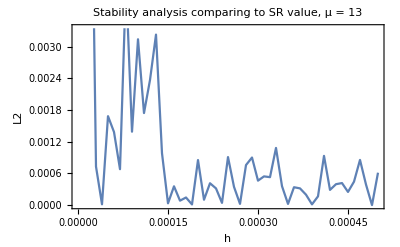

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.96232596194969)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 13 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{13,0.962291,0.00966751}

```mathematica
ld = {{0.000030000000000000004,0.9615953195424767},{0.00004,0.9623094204234279},{0.00005,0.9606424422878445},{0.00006,0.9637095776422733},{0.00007000000000000001,0.9616452568815025},{0.00008,0.9580964929547199},{0.00009,0.963715696333847},{0.0001,0.9591881820526376},{0.00011,0.964068290386425},{0.00012,0.9646935133432916},{0.00013000000000000002,0.9655520781487698},{0.00014000000000000001,0.9613439440795452},{0.00015000000000000001,0.962290973051771},{0.00016,0.9619689831654936},{0.00017,0.9622406718072721},{0.00018,0.9621805514711756},{0.00019,0.9623399222482083},{0.0002,0.9631793726900316},{0.00021,0.9622232313158473},{0.00022,0.9627406691189568},{0.00023,0.9626432057582381},{0.00024,0.9622826717424847},{0.00025,0.9632356208169328},{0.00026000000000000003,0.9626729070058991},{0.00027000000000000006,0.9623015546780693},{0.0002800000000000001,0.9630845215432836},{0.00029000000000000006,0.9614246655784661},{0.00030000000000000003,0.9627898793161577},{0.00031000000000000005,0.9617815132942834},{0.00032,0.9617961095496947},{0.00033000000000000005,0.9634086520298696},{0.0003400000000000001,0.9626855984365486},{0.00035000000000000005,0.9623022014026206},{0.0003600000000000001,0.961986644498589},{0.0003700000000000001,0.9620083398986188},{0.0003800000000000001,0.962524637753704},{0.00039000000000000005,0.9623415402526053},{0.0004000000000000001,0.9624930236487647},{0.00041000000000000005,0.9613935875362398},{0.00042000000000000007,0.9620367477212927},{0.0004300000000000001,0.961929183224787},{0.00044000000000000007,0.9627441281407587},{0.00045000000000000004,0.962075336859506},{0.00046000000000000007,0.9618813612197237},{0.00047000000000000004,0.9614699999281829},{0.00048000000000000007,0.9619355524732469},{0.0004900000000000001,0.9623276009113432},{0.0005000000000000001,0.9617118109994378}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.962271

0.00116666

### μ = 14

```mathematica
p= 4;
μ=14;
M :=0.004566912864548285
ϕini =6.814015478827032;
ϕend=13.343026800200992;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,5.7 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  5.7 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      5.7 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

5.68065×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.962447},{0.00002,0.965441},{0.00003,0.952918},{0.00004,0.969839},{0.00005,0.960573},{0.00006,0.968486},{0.00007,0.962829},{0.00008,0.961443},{0.00009,0.965594},{0.0001,0.963243},{0.00011,0.963441},{0.00012,0.964799},{0.00013,0.964183},{0.00014,0.963701},{0.00015,0.962418},{0.00016,0.962666},{0.00017,0.964571},{0.00018,0.966225},{0.00019,0.965291},{0.0002,0.962744},{0.00021,0.964716},{0.00022,0.96246},{0.00023,0.963415},{0.00024,0.962629},{0.00025,0.962755},{0.00026,0.962649},{0.00027,0.962885},{0.00028,0.963787},{0.00029,0.964353},{0.0003,0.963545},{0.00031,0.962906},{0.00032,0.963136},{0.00033,0.963221},{0.00034,0.963727},{0.00035,0.962081},{0.00036,0.96301},{0.00037,0.963311},{0.00038,0.962952},{0.00039,0.963285},{0.0004,0.962158},{0.00041,0.962135},{0.00042,0.962595},{0.00043,0.962729},{0.00044,0.963186},{0.00045,0.962053},{0.00046,0.962169},{0.00047,0.963198},{0.00048,0.962994},{0.00049,0.963663},{0.0005,0.962921}}

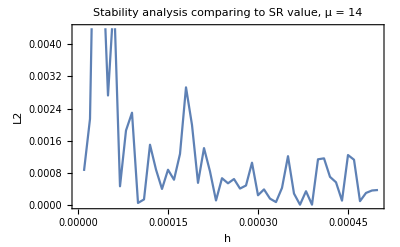

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9632981450445992)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 14 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{14,0.962418,0.0111859}

```mathematica
ld ={{0.00001,0.9624470709304976},{0.00002,0.9654405844683774},{0.000030000000000000004,0.9529175267993361},{0.00004,0.9698392254118193},{0.00005,0.9605733206050492},{0.00006,0.9684855074499963},{0.00007000000000000001,0.9628288608687374},{0.00008,0.9614426483816482},{0.00009,0.9655943710042515},{0.0001,0.9632430978164838},{0.00011,0.9634412563823124},{0.00012,0.9647993042615244},{0.00013000000000000002,0.9641825511891791},{0.00014000000000000001,0.9637012566108467},{0.00015000000000000001,0.9624180438009775},{0.00016,0.9626659395572361},{0.00017,0.9645714588651849},{0.00018,0.9662250173898683},{0.00019,0.9652907026252108},{0.0002,0.9627438038970695},{0.00021,0.9647164657719647},{0.00022,0.9624599519724852},{0.00023,0.963414936085853},{0.00024,0.9626285507782606},{0.00025,0.9627546184681066},{0.00026000000000000003,0.9626488659085947},{0.00027000000000000006,0.9628851977920798},{0.0002800000000000001,0.9637867746170411},{0.00029000000000000006,0.9643534821886622},{0.00030000000000000003,0.9635445176072506},{0.00031000000000000005,0.962906180148261},{0.00032,0.9631357574975078},{0.00033000000000000005,0.9632211043100178},{0.0003400000000000001,0.9637274244015919},{0.00035000000000000005,0.96208133969317},{0.0003600000000000001,0.9630101186037892},{0.0003700000000000001,0.9633106202148274},{0.0003800000000000001,0.9629518292437753},{0.00039000000000000005,0.9632852276083361},{0.0004000000000000001,0.9621583946564418},{0.00041000000000000005,0.9621351014777608},{0.00042000000000000007,0.9625947572509627},{0.0004300000000000001,0.9627294078298574},{0.00044000000000000007,0.9631858354617769},{0.00045000000000000004,0.9620526111944384},{0.00046000000000000007,0.9621689328959029},{0.00047000000000000004,0.9631981494168304},{0.00048000000000000007,0.9629943722662608},{0.0004900000000000001,0.9636628174682828},{0.0005000000000000001,0.9629213988829198}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.96327

0.0021767

### μ = 15

```mathematica
p= 4;
μ=15;
M :=0.004723855720072838
ϕini =7.611201120172861;
ϕend=14.33988870618899;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,5.4 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  5.4 10^6}, MaxStepSize->100,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      5.4 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

5.37255×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.982058},{0.00002,0.96858},{0.00003,0.963817},{0.00004,0.962881},{0.00005,0.964216},{0.00006,0.963166},{0.00007,0.965561},{0.00008,0.964467},{0.00009,0.963048},{0.0001,0.963115},{0.00011,0.965697},{0.00012,0.964089},{0.00013,0.963893},{0.00014,0.963795},{0.00015,0.963452},{0.00016,0.964458},{0.00017,0.965603},{0.00018,0.965131},{0.00019,0.965061},{0.0002,0.963883},{0.00021,0.964675},{0.00022,0.964774},{0.00023,0.964839},{0.00024,0.964567},{0.00025,0.963782},{0.00026,0.96385},{0.00027,0.964992},{0.00028,0.964514},{0.00029,0.96393},{0.0003,0.964107},{0.00031,0.963019},{0.00032,0.96498},{0.00033,0.964487},{0.00034,0.96434},{0.00035,0.96423},{0.00036,0.963505},{0.00037,0.963957},{0.00038,0.96473},{0.00039,0.964084},{0.0004,0.964238},{0.00041,0.963745},{0.00042,0.964103},{0.00043,0.964336},{0.00044,0.963768},{0.00045,0.96334},{0.00046,0.96348},{0.00047,0.963639},{0.00048,0.963942},{0.00049,0.964077},{0.0005,0.963967}}

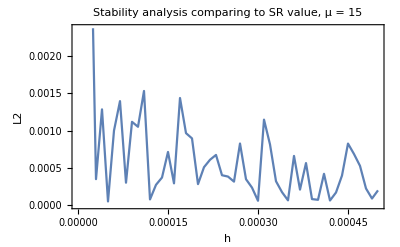

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.964165731144023)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 15 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{15,0.963452,0.0127078}

```mathematica
ld = {{0.00002,0.9685803640365362},{0.000030000000000000004,0.9638167109080783},{0.00004,0.9628809700894038},{0.00005,0.9642157068242934},{0.00006,0.9631656948415225},{0.00007000000000000001,0.965560819455011},{0.00008,0.9644670408731328},{0.00009,0.963048238188658},{0.0001,0.9631147678634274},{0.00011,0.965697164616114},{0.00012,0.9640885961714312},{0.00013000000000000002,0.9638927565066756},{0.00014000000000000001,0.9637950421178451},{0.00015000000000000001,0.9634523473550928},{0.00016,0.9644583881139475},{0.00017,0.9656026730816817},{0.00018,0.9651314932496043},{0.00019,0.9650612392187622},{0.0002,0.9638834892728406},{0.00021,0.9646749576905485},{0.00022,0.9647743012934976},{0.00023,0.9648393134300399},{0.00024,0.9645673238851548},{0.00025,0.9637822052328393},{0.00026000000000000003,0.9638500006378823},{0.00027000000000000006,0.9649924224040646},{0.0002800000000000001,0.9645141568943799},{0.00029000000000000006,0.9639302834396719},{0.00030000000000000003,0.9641067481252192},{0.00031000000000000005,0.9630189143518215},{0.00032,0.964980184539359},{0.00033000000000000005,0.9644867519403919},{0.0003400000000000001,0.9643404259998664},{0.00035000000000000005,0.9642304628718196},{0.0003600000000000001,0.9635054449821555},{0.0003700000000000001,0.963956869167536},{0.0003800000000000001,0.9647300960781755},{0.00039000000000000005,0.9640842528037296},{0.0004000000000000001,0.9642376465639044},{0.00041000000000000005,0.9637451467778855},{0.00042000000000000007,0.9641029698051856},{0.0004300000000000001,0.9643357392466737},{0.00044000000000000007,0.9637683165552391},{0.00045000000000000004,0.9633397942451803},{0.00046000000000000007,0.9634800274571454},{0.00047000000000000004,0.9636387135928892},{0.00048000000000000007,0.9639419632364812},{0.0004900000000000001,0.964076683184168},{0.0005000000000000001,0.9639670891099608}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.964243

0.000919401

### μ = 16

```mathematica
p= 4;
μ=16;
M :=0.0048690074110789095
ϕini =8.427177619183134;
ϕend=15.337120009797683;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,5.12 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  5.12 10^6}, MaxStepSize->100,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      5.12 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

5.11735×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.969393},{0.00002,0.960585},{0.00003,0.96501},{0.00004,0.959419},{0.00005,0.961663},{0.00006,0.96669},{0.00007,0.966635},{0.00008,0.965813},{0.00009,0.963468},{0.0001,0.966547},{0.00011,0.964962},{0.00012,0.965705},{0.00013,0.965349},{0.00014,0.964339},{0.00015,0.965487},{0.00016,0.964034},{0.00017,0.964836},{0.00018,0.966747},{0.00019,0.966089},{0.0002,0.964241},{0.00021,0.964181},{0.00022,0.965788},{0.00023,0.965601},{0.00024,0.965749},{0.00025,0.964768},{0.00026,0.964858},{0.00027,0.96476},{0.00028,0.965748},{0.00029,0.965453},{0.0003,0.965753},{0.00031,0.964556},{0.00032,0.964996},{0.00033,0.964484},{0.00034,0.965667},{0.00035,0.965254},{0.00036,0.964986},{0.00037,0.964557},{0.00038,0.964158},{0.00039,0.964781},{0.0004,0.965175},{0.00041,0.965236},{0.00042,0.96439},{0.00043,0.96439},{0.00044,0.964993},{0.00045,0.964963},{0.00046,0.96518},{0.00047,0.964283},{0.00048,0.964344},{0.00049,0.964112},{0.0005,0.964917}}

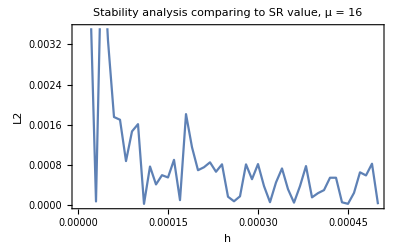

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9649360408810884)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 16 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{16,0.965487,0.0142154}

```mathematica
ld = {{0.00001,0.9693927485114678},{0.00002,0.9605845755729154},{0.000030000000000000004,0.9650101654056814},{0.00004,0.9594189087295821},{0.00005,0.9616631548233103},{0.00006,0.9666897515418339},{0.00007000000000000001,0.9666350360649169},{0.00008,0.9658130550597437},{0.00009,0.963468184893089},{0.0001,0.966547458893076},{0.00011,0.9649620977161734},{0.00012,0.9657051065575862},{0.00013000000000000002,0.9653486818094807},{0.00014000000000000001,0.9643392998229201},{0.00015000000000000001,0.965487327386421},{0.00016,0.9640344129865707},{0.00017,0.9648358032253211},{0.00018,0.9667472589610693},{0.00019,0.9660888158812168},{0.0002,0.964240618780501},{0.00021,0.9641811415137211},{0.00022,0.9657884534382455},{0.00023,0.9656011451122853},{0.00024,0.9657489027802197},{0.00025,0.9647682296545796},{0.00026000000000000003,0.9648584583828611},{0.00027000000000000006,0.9647599090667024},{0.0002800000000000001,0.965747821181221},{0.00029000000000000006,0.9654527974965842},{0.00030000000000000003,0.965753427425247},{0.00031000000000000005,0.9645559838130268},{0.00032,0.9649956105653958},{0.00033000000000000005,0.9644839311178867},{0.0003400000000000001,0.9656665078737132},{0.00035000000000000005,0.9652543186237121},{0.0003600000000000001,0.9649864261403382},{0.0003700000000000001,0.9645567555592063},{0.0003800000000000001,0.9641583107478051},{0.00039000000000000005,0.9647808242900112},{0.0004000000000000001,0.9651751346052431},{0.00041000000000000005,0.9652355912926288},{0.00042000000000000007,0.9643900634920073},{0.0004300000000000001,0.964390207745605},{0.00044000000000000007,0.9649931412053762},{0.00045000000000000004,0.9649629038145026},{0.00046000000000000007,0.9651804927527952},{0.00047000000000000004,0.9642825277719903},{0.00048000000000000007,0.9643441677952214},{0.0004900000000000001,0.9641115567258058},{0.0005000000000000001,0.9649172908058127}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.964902

0.00147636

### μ = 17

```mathematica
p= 4;
μ=17;
M :=0.005003786067572624
ϕini =9.259672270138136;
ϕend=16.334659157652062;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4.91 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  4.91 10^6}, MaxStepSize->100,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      4.91 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

4.90323×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.971513},{0.00002,0.963756},{0.00003,0.961981},{0.00004,0.961563},{0.00005,0.966076},{0.00006,0.965363},{0.00007,0.966794},{0.00008,0.965053},{0.00009,0.965087},{0.0001,0.966215},{0.00011,0.966336},{0.00012,0.965701},{0.00013,0.966315},{0.00014,0.966282},{0.00015,0.965556},{0.00016,0.965226},{0.00017,0.965508},{0.00018,0.965401},{0.00019,0.966241},{0.0002,0.965601},{0.00021,0.965231},{0.00022,0.96607},{0.00023,0.965658},{0.00024,0.965203},{0.00025,0.965496},{0.00026,0.966685},{0.00027,0.965168},{0.00028,0.965294},{0.00029,0.96561},{0.0003,0.965176},{0.00031,0.966971},{0.00032,0.965517},{0.00033,0.965817},{0.00034,0.965805},{0.00035,0.96532},{0.00036,0.965659},{0.00037,0.965848},{0.00038,0.96578},{0.00039,0.966049},{0.0004,0.965268},{0.00041,0.96577},{0.00042,0.965376},{0.00043,0.965348},{0.00044,0.965352},{0.00045,0.965099},{0.00046,0.9651},{0.00047,0.965186},{0.00048,0.965459},{0.00049,0.965635},{0.0005,0.965314}}

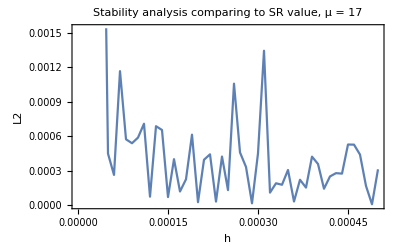

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9656267948926345)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 17 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{17,0.965556,0.0157046}

```mathematica
ld = {{0.00001,0.9715129722043674},{0.00002,0.963756238697621},{0.000030000000000000004,0.9619810757418096},{0.00004,0.9615634678115248},{0.00005,0.9660755732614305},{0.00006,0.9653632449908515},{0.00007000000000000001,0.9667939361542057},{0.00008,0.9650531255804377},{0.00009,0.9650873937248379},{0.0001,0.966215070325251},{0.00011,0.9663360814166213},{0.00012,0.9657007785088755},{0.00013000000000000002,0.9663145329048166},{0.00014000000000000001,0.966281506623512},{0.00015000000000000001,0.965556215093907},{0.00016,0.9652262129962452},{0.00017,0.965507664320344},{0.00018,0.9654011640010454},{0.00019,0.9662408404191953},{0.0002,0.9656007363397903},{0.00021,0.9652313084223643},{0.00022,0.9660695694368715},{0.00023,0.9656580326169046},{0.00024,0.9652034379289778},{0.00025,0.9654956575073872},{0.00026000000000000003,0.9666849728975727},{0.00027000000000000006,0.9651675621033173},{0.0002800000000000001,0.965294065890467},{0.00029000000000000006,0.9656104562272515},{0.00030000000000000003,0.965175500974044},{0.00031000000000000005,0.9669714719274316},{0.00032,0.9655174213976714},{0.00033000000000000005,0.9658173960451693},{0.0003400000000000001,0.9658046487680402},{0.00035000000000000005,0.9653202614244464},{0.0003600000000000001,0.9656586496357075},{0.0003700000000000001,0.9658479888925265},{0.0003800000000000001,0.9657799831524572},{0.00039000000000000005,0.9660493473648852},{0.0004000000000000001,0.9652679745825034},{0.00041000000000000005,0.9657700551211579},{0.00042000000000000007,0.9653764629631251},{0.0004300000000000001,0.9653478676604431},{0.00044000000000000007,0.9653520888982433},{0.00045000000000000004,0.9650987398389593},{0.00046000000000000007,0.9650996465864876},{0.00047000000000000004,0.965186199519865},{0.00048000000000000007,0.9654593181519338},{0.0004900000000000001,0.9656347336014955},{0.0005000000000000001,0.9653144584607439}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.965577

0.00126258

### μ = 18

```mathematica
p= 4;
μ=18;
M :=0.005129415924869072
ϕini =10.106728678999152;
ϕend=17.332457543904017;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4.75 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  4.75 10^6}, MaxStepSize->50,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      4.75 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
Plot[a[t],{t,0,tend+0.0510^6}, PlotRange->All, Frame->True, FrameLabel->{"t", "a(t)"}]
```

-Graphics-

```mathematica
tend
```

4.72151×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.977299},{0.00002,0.972045},{0.00003,0.963903},{0.00004,0.964566},{0.00005,0.967151},{0.00006,0.963587},{0.00007,0.968165},{0.00008,0.969542},{0.00009,0.966663},{0.0001,0.964447},{0.00011,0.963811},{0.00012,0.967659},{0.00013,0.966056},{0.00014,0.966242},{0.00015,0.966487},{0.00016,0.965959},{0.00017,0.965511},{0.00018,0.967073},{0.00019,0.968655},{0.0002,0.96639},{0.00021,0.96652},{0.00022,0.966718},{0.00023,0.964902},{0.00024,0.966239},{0.00025,0.966601},{0.00026,0.967112},{0.00027,0.966952},{0.00028,0.966916},{0.00029,0.966657},{0.0003,0.966798},{0.00031,0.966635},{0.00032,0.96664},{0.00033,0.965815},{0.00034,0.965963},{0.00035,0.965516},{0.00036,0.966397},{0.00037,0.966588},{0.00038,0.965799},{0.00039,0.965689},{0.0004,0.966194},{0.00041,0.966207},{0.00042,0.965623},{0.00043,0.966046},{0.00044,0.966015},{0.00045,0.965697},{0.00046,0.965746},{0.00047,0.96649},{0.00048,0.965796},{0.00049,0.966809},{0.0005,0.9661}}

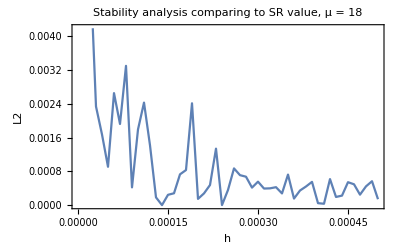

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9662410882957015)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 18 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{18,0.966487,0.0171634}

```mathematica
ld = {{0.00001,0.9772987647223336},{0.00002,0.9720448360409},{0.000030000000000000004,0.9639026347049097},{0.00004,0.9645658669819522},{0.00005,0.967150776208482},{0.00006,0.9635865324826413},{0.00007000000000000001,0.9681648210720984},{0.00008,0.9695421287112947},{0.00009,0.966662765691105},{0.0001,0.9644473828088119},{0.00011,0.9638112822509604},{0.00012,0.9676590610284744},{0.00013000000000000002,0.9660563610865289},{0.00014000000000000001,0.9662423868044859},{0.00015000000000000001,0.9664866711585253},{0.00016,0.9659592250889888},{0.00017,0.9655105007987036},{0.00018,0.9670732818143285},{0.00019,0.9686550370869199},{0.0002,0.9663901786209956},{0.00021,0.9665202792091564},{0.00022,0.9667182439238832},{0.00023,0.9649019865844337},{0.00024,0.9662386798337921},{0.00025,0.966601447419193},{0.00026000000000000003,0.9671124345635013},{0.00027000000000000006,0.9669522389276431},{0.0002800000000000001,0.9669155888561928},{0.00029000000000000006,0.966657466916682},{0.00030000000000000003,0.9667979376565534},{0.00031000000000000005,0.9666350311032006},{0.00032,0.9666399396983464},{0.00033000000000000005,0.9658148427084515},{0.0003400000000000001,0.9659628276258289},{0.00035000000000000005,0.965516203651576},{0.0003600000000000001,0.9663973308362912},{0.0003700000000000001,0.966588464020433},{0.0003800000000000001,0.9657986960771517},{0.00039000000000000005,0.9656889608640021},{0.0004000000000000001,0.9661936078549559},{0.00041000000000000005,0.9662072396713703},{0.00042000000000000007,0.9656231339677959},{0.0004300000000000001,0.9660462196302971},{0.00044000000000000007,0.9660147410260179},{0.00045000000000000004,0.9656965875100376},{0.00046000000000000007,0.9657462247437428},{0.00047000000000000004,0.9664902932717074},{0.00048000000000000007,0.9657955395158494},{0.0004900000000000001,0.9668085274068876},{0.0005000000000000001,0.9660998108175124}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.966568

0.00205892

### μ = 19

```mathematica
p= 4;
μ=19;
M :=0.005246953375504309
ϕini =10.96666075778189;
ϕend=18.330476277859745;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4.57 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  4.57 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      4.57 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

4.56574×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.931071},{0.00002,0.956757},{0.00003,0.967553},{0.00004,0.975848},{0.00005,0.972083},{0.00006,0.967764},{0.00007,0.965631},{0.00008,0.964319},{0.00009,0.960131},{0.0001,0.965912},{0.00011,0.968438},{0.00012,0.969515},{0.00013,0.96737},{0.00014,0.96507},{0.00015,0.964242},{0.00016,0.969173},{0.00017,0.968247},{0.00018,0.968119},{0.00019,0.966395},{0.0002,0.966859},{0.00021,0.967192},{0.00022,0.96521},{0.00023,0.968179},{0.00024,0.970811},{0.00025,0.966525},{0.00026,0.966166},{0.00027,0.967449},{0.00028,0.96594},{0.00029,0.967093},{0.0003,0.96755},{0.00031,0.967141},{0.00032,0.965745},{0.00033,0.964402},{0.00034,0.966636},{0.00035,0.966862},{0.00036,0.967488},{0.00037,0.967449},{0.00038,0.966609},{0.00039,0.966742},{0.0004,0.966297},{0.00041,0.967134},{0.00042,0.96603},{0.00043,0.967529},{0.00044,0.966695},{0.00045,0.966252},{0.00046,0.966554},{0.00047,0.966321},{0.00048,0.967091},{0.00049,0.966835},{0.0005,0.966601}}

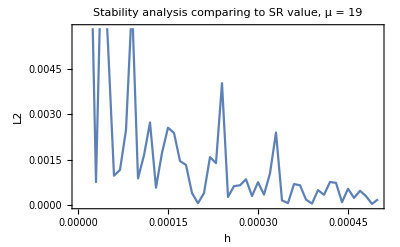

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9667934715589722)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 19 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
h2 = 0.00016;
{μ, nS[0.002],r[0.002]}
```

{19,0.966999,0.0185788}

```mathematica
ld  = {{0.00002,0.9567571171822464},{0.000030000000000000004,0.9675527696818802},{0.00004,0.9758476731880152},{0.00005,0.972083440158574},{0.00006,0.9677641484809234},{0.00007000000000000001,0.9656312545508678},{0.00008,0.9643187476576475},{0.00009,0.9601305015267958},{0.0001,0.965911753635968},{0.00011,0.9684378062177038},{0.00012,0.9695154155656857},{0.00013000000000000002,0.9673703301309833},{0.00014000000000000001,0.965070432911329},{0.00015000000000000001,0.9642420287513588},{0.00016,0.9691730652874658},{0.00017,0.9682470528184778},{0.00018,0.9681191842579522},{0.00019,0.9663952211696926},{0.0002,0.9668585697936231},{0.00021,0.9671923493148358},{0.00022,0.9652101361020649},{0.00023,0.9681785775290519},{0.00024,0.9708112916107644},{0.00025,0.9665249392215177},{0.00026000000000000003,0.966166095578185},{0.00027000000000000006,0.9674487985045849},{0.0002800000000000001,0.965940305459119},{0.00029000000000000006,0.9670927755349393},{0.00030000000000000003,0.9675503114173574},{0.00031000000000000005,0.9671406383078971},{0.00032,0.9657450176812202},{0.00033000000000000005,0.9644015667714815},{0.0003400000000000001,0.9666360185113876},{0.00035000000000000005,0.9668620048176506},{0.0003600000000000001,0.9674884836955969},{0.0003700000000000001,0.9674491660374617},{0.0003800000000000001,0.9666089182027},{0.00039000000000000005,0.9667418888068879},{0.0004000000000000001,0.9662968707348165},{0.00041000000000000005,0.9671344293027473},{0.00042000000000000007,0.9660302188871875},{0.0004300000000000001,0.9675285764852773},{0.00044000000000000007,0.9666952032667112},{0.00045000000000000004,0.9662520313353539},{0.00046000000000000007,0.9665535206738229},{0.00047000000000000004,0.9663206526057547},{0.00048000000000000007,0.9670911586541889},{0.0004900000000000001,0.9668350290823436},{0.0005000000000000001,0.9666013779040395}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.966815

0.0026124

### μ = 20

```mathematica
p= 4;
μ=20;
M :=0.005357305723288271
ϕini =11.838012784632001;
ϕend=19.328683873439395;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4.45 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  4.56 10^6}, MaxStepSize->200,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      4.45 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

4.43099×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.963149},{0.00002,0.961176},{0.00003,0.964773},{0.00004,0.976669},{0.00005,0.974512},{0.00006,0.971232},{0.00007,0.972155},{0.00008,0.966603},{0.00009,0.967521},{0.0001,0.97183},{0.00011,0.967412},{0.00012,0.968994},{0.00013,0.967922},{0.00014,0.968882},{0.00015,0.966626},{0.00016,0.967627},{0.00017,0.969824},{0.00018,0.969067},{0.00019,0.968922},{0.0002,0.968184},{0.00021,0.966766},{0.00022,0.968138},{0.00023,0.969007},{0.00024,0.967775},{0.00025,0.965776},{0.00026,0.967027},{0.00027,0.966461},{0.00028,0.967075},{0.00029,0.966377},{0.0003,0.967893},{0.00031,0.967112},{0.00032,0.967542},{0.00033,0.966432},{0.00034,0.968104},{0.00035,0.967251},{0.00036,0.967915},{0.00037,0.967135},{0.00038,0.965517},{0.00039,0.966878},{0.0004,0.967859},{0.00041,0.96593},{0.00042,0.96693},{0.00043,0.96716},{0.00044,0.967849},{0.00045,0.966752},{0.00046,0.966975},{0.00047,0.966021},{0.00048,0.966629},{0.00049,0.966182},{0.0005,0.966731}}

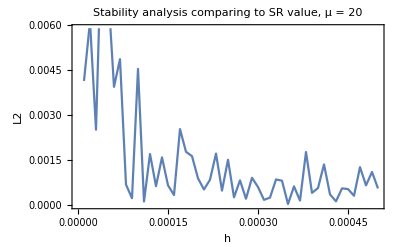

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9672887071909434)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 20 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{20,0.967768,0.0199592}

```mathematica
ld = {{0.00001,0.9631487336221065},{0.00002,0.9611756192481283},{0.000030000000000000004,0.9647732189185473},{0.00004,0.9766686315984393},{0.00005,0.9745115128056059},{0.00006,0.971232316064787},{0.00007000000000000001,0.9721552304312194},{0.00008,0.9666026898230908},{0.00009,0.9675207611707956},{0.0001,0.9718303130566784},{0.00011,0.9674115116108647},{0.00012,0.9689938345975788},{0.00013000000000000002,0.9679223351856668},{0.00014000000000000001,0.9688816310480205},{0.00015000000000000001,0.9666258694236249},{0.00016,0.9676268272037429},{0.00017,0.9698238206008444},{0.00018,0.9690672444447522},{0.00019,0.9689219544814096},{0.0002,0.9681836986196983},{0.00021,0.966765989186107},{0.00022,0.9681377585865308},{0.00023,0.969007038100738},{0.00024,0.967774822792697},{0.00025,0.9657760958125525},{0.00026000000000000003,0.9670271832243139},{0.00027000000000000006,0.9664613449260283},{0.0002800000000000001,0.967074590204606},{0.00029000000000000006,0.9663766989161302},{0.00030000000000000003,0.9678934851469614},{0.00031000000000000005,0.9671116553137445},{0.00032,0.9675415270138289},{0.00033000000000000005,0.9664317580013834},{0.0003400000000000001,0.9681039088757378},{0.00035000000000000005,0.9672511178712119},{0.0003600000000000001,0.9679153897289335},{0.0003700000000000001,0.9671352955190984},{0.0003800000000000001,0.9655171065080481},{0.00039000000000000005,0.9668782812101298},{0.0004000000000000001,0.9678591031620906},{0.00041000000000000005,0.965930094175516},{0.00042000000000000007,0.9669295218716062},{0.0004300000000000001,0.9671602909700395},{0.00044000000000000007,0.9678493439567233},{0.00045000000000000004,0.9667522360079708},{0.00046000000000000007,0.9669748579569375},{0.00047000000000000004,0.9660209581611513},{0.00048000000000000007,0.9666287315708786},{0.0004900000000000001,0.9661824335888781},{0.0005000000000000001,0.9667310033643427}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.967686

0.00244639

### μ = 30

```mathematica
p= 4;
μ=30;
M :=0.006196164886288982
ϕini =20.968696887654183;
ϕend=29.317124882378216;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.7 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.7 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3.7 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.69425×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.967142},{0.00002,0.961905},{0.00003,0.969721},{0.00004,0.97165},{0.00005,0.981605},{0.00006,0.974668},{0.00007,0.970716},{0.00008,0.970084},{0.00009,0.972246},{0.0001,0.965205},{0.00011,0.967289},{0.00012,0.96819},{0.00013,0.966054},{0.00014,0.970796},{0.00015,0.970243},{0.00016,0.967206},{0.00017,0.969976},{0.00018,0.970063},{0.00019,0.967091},{0.0002,0.970682},{0.00021,0.970545},{0.00022,0.972292},{0.00023,0.971537},{0.00024,0.971893},{0.00025,0.970095},{0.00026,0.970026},{0.00027,0.96921},{0.00028,0.970623},{0.00029,0.975851},{0.0003,0.971938},{0.00031,0.96939},{0.00032,0.965232},{0.00033,0.970168},{0.00034,0.967545},{0.00035,0.970101},{0.00036,0.968286},{0.00037,0.969031},{0.00038,0.970783},{0.00039,0.97256},{0.0004,0.969828},{0.00041,0.969521},{0.00042,0.969394},{0.00043,0.969625},{0.00044,0.970555},{0.00045,0.970684},{0.00046,0.970731},{0.00047,0.969775},{0.00048,0.969892},{0.00049,0.96907},{0.0005,0.969327}}

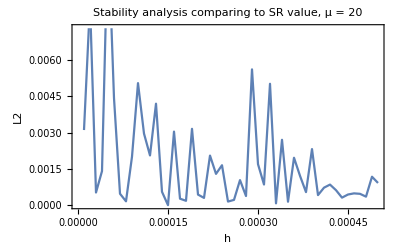

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9702440720589285)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 20 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{30,0.970243,0.0312475}

```mathematica
ld = {{0.00001,0.967141735615399},{0.00002,0.9619046945921491},{0.000030000000000000004,0.969720847992329},{0.00004,0.9716503562588985},{0.00005,0.9816049144894883},{0.00006,0.9746676878474019},{0.00007000000000000001,0.9707163378390432},{0.00008,0.9700842942780764},{0.00009,0.9722463243147907},{0.0001,0.9652049463485712},{0.00011,0.967288918481446},{0.00012,0.9681902021060552},{0.00013000000000000002,0.9660538166312842},{0.00014000000000000001,0.9707962296149577},{0.00015000000000000001,0.9702430965626803},{0.00016,0.9672064559927019},{0.00017,0.9699759021057659},{0.00018,0.9700632064361733},{0.00019,0.9670911945903105},{0.0002,0.9706815120473061},{0.00021,0.9705445077648376},{0.00022,0.9722919114019121},{0.00023,0.9715366828302839},{0.00024,0.9718932266440526},{0.00025,0.9700951535692615},{0.00026000000000000003,0.9700255222391275},{0.00027000000000000006,0.9692095787265872},{0.0002800000000000001,0.9706231492832746},{0.00029000000000000006,0.9758511823941083},{0.00030000000000000003,0.9719376701951683},{0.00031000000000000005,0.9693904827884768},{0.00032,0.9652322067443612},{0.00033000000000000005,0.9701683713808681},{0.0003400000000000001,0.9675445840332847},{0.00035000000000000005,0.9701014741244509},{0.0003600000000000001,0.9682857786153642},{0.0003700000000000001,0.9690310546859974},{0.0003800000000000001,0.9707827393194484},{0.00039000000000000005,0.9725600877829137},{0.0004000000000000001,0.9698279272302385},{0.00041000000000000005,0.9695214412695597},{0.00042000000000000007,0.9693944634645904},{0.0004300000000000001,0.9696250790196279},{0.00044000000000000007,0.9705552391823253},{0.00045000000000000004,0.9706844870693222},{0.00046000000000000007,0.9707314573569077},{0.00047000000000000004,0.9697752511743528},{0.00048000000000000007,0.9698924591862367},{0.0004900000000000001,0.9690695879102064},{0.0005000000000000001,0.9693270785269903}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.969961

0.00285448

### μ = 40

```mathematica
p= 4;
μ=40;
M :=0.006770526977317428
ϕini =30.502237811684925;
ϕend=39.311208595672355;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.4 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.4 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3.4 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.39816×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,1.02076},{0.00002,1.00177},{0.00003,0.991918},{0.00004,0.98299},{0.00005,0.964198},{0.00006,0.935985},{0.00007,0.96991},{0.00008,0.955243},{0.00009,0.966301},{0.0001,0.973302},{0.00011,0.978324},{0.00012,0.974536},{0.00013,0.979661},{0.00014,0.97563},{0.00015,0.97045},{0.00016,0.972526},{0.00017,0.975072},{0.00018,0.971926},{0.00019,0.9759},{0.0002,0.972298},{0.00021,0.972546},{0.00022,0.971132},{0.00023,0.974287},{0.00024,0.971055},{0.00025,0.973195},{0.00026,0.978478},{0.00027,0.972657},{0.00028,0.970502},{0.00029,0.964149},{0.0003,0.970429},{0.00031,0.972646},{0.00032,0.970548},{0.00033,0.974066},{0.00034,0.971188},{0.00035,0.972074},{0.00036,0.97197},{0.00037,0.968672},{0.00038,0.97135},{0.00039,0.97474},{0.0004,0.967441},{0.00041,0.970395},{0.00042,0.972049},{0.00043,0.970881},{0.00044,0.970879},{0.00045,0.976366},{0.00046,0.971906},{0.00047,0.971902},{0.00048,0.971864},{0.00049,0.971822},{0.0005,0.971053}}

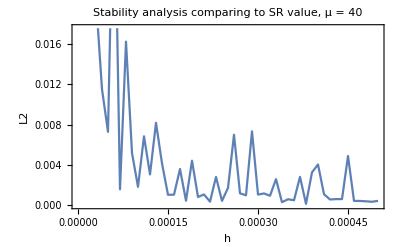

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9714822241513937)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 40 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{40,0.97045,0.0388562}

```mathematica
ld = {{0.00004,0.9829899825964307},{0.00005,0.9641976282687201},{0.00006,0.9359852934096292},{0.00007000000000000001,0.9699102515424725},{0.00008,0.9552429243640673},{0.00009,0.966300720246026},{0.0001,0.9733024847899017},{0.00011,0.9783239211646783},{0.00012,0.9745356117989354},{0.00013000000000000002,0.9796606415815683},{0.00014000000000000001,0.9756300949049962},{0.00015000000000000001,0.9704495368706039},{0.00016,0.972526264092344},{0.00017,0.9750719442028224},{0.00018,0.9719264101210141},{0.00019,0.9759002279882601},{0.0002,0.9722983170254612},{0.00021,0.9725460384546644},{0.00022,0.9711317841578923},{0.00023,0.9742869158846126},{0.00024,0.9710551163705423},{0.00025,0.9731946688943413},{0.00026000000000000003,0.9784781160646133},{0.00027000000000000006,0.9726571330525902},{0.0002800000000000001,0.9705023466658285},{0.00029000000000000006,0.9641490335986906},{0.00030000000000000003,0.9704288656972841},{0.00031000000000000005,0.9726458320463811},{0.00032,0.9705483936258938},{0.00033000000000000005,0.9740661864007355},{0.0003400000000000001,0.971188078396876},{0.00035000000000000005,0.9720737665407737},{0.0003600000000000001,0.9719704351295347},{0.0003700000000000001,0.9686720292158459},{0.0003800000000000001,0.9713503952536393},{0.00039000000000000005,0.9747400369058583},{0.0004000000000000001,0.9674406537316942},{0.00041000000000000005,0.9703947489493262},{0.00042000000000000007,0.9720491927885746},{0.0004300000000000001,0.9708806064473167},{0.00044000000000000007,0.9708785512535961},{0.00045000000000000004,0.9763656981643143},{0.00046000000000000007,0.9719063043579758},{0.00047000000000000004,0.9719021118475111},{0.00048000000000000007,0.971864256375836},{0.0004900000000000001,0.9718215510726278},{0.0005000000000000001,0.9710534913940779}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.971202

0.00676236

```mathematica
0.03885616951315774
```

### μ = 50

```mathematica
p= 4;
μ=50;
M :=0.007216166689485368
ϕini =40.21406574970534;
ϕend=49.30761412424262;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.3 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.3 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3.2 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.24228×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.927869},{0.00002,0.962905},{0.00003,0.961729},{0.00004,0.958292},{0.00005,0.976766},{0.00006,0.975775},{0.00007,0.975097},{0.00008,0.982127},{0.00009,0.966973},{0.0001,0.961923},{0.00011,0.982721},{0.00012,0.969362},{0.00013,0.979687},{0.00014,0.975375},{0.00015,0.967724},{0.00016,0.972098},{0.00017,0.969637},{0.00018,0.970781},{0.00019,0.973855},{0.0002,0.969638},{0.00021,0.968988},{0.00022,0.967311},{0.00023,0.971088},{0.00024,0.975165},{0.00025,0.970994},{0.00026,0.970509},{0.00027,0.972453},{0.00028,0.97401},{0.00029,0.973785},{0.0003,0.972225},{0.00031,0.969659},{0.00032,0.967094},{0.00033,0.974832},{0.00034,0.971286},{0.00035,0.972664},{0.00036,0.974342},{0.00037,0.973433},{0.00038,0.973057},{0.00039,0.968035},{0.0004,0.971845},{0.00041,0.972406},{0.00042,0.971267},{0.00043,0.97222},{0.00044,0.972148},{0.00045,0.973648},{0.00046,0.973005},{0.00047,0.968557},{0.00048,0.972488},{0.00049,0.970315},{0.0005,0.970434}}

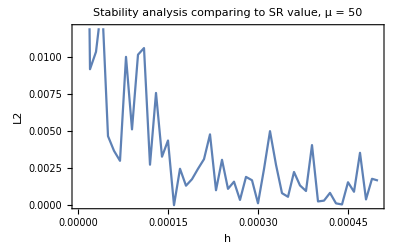

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9720983264780103)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{50,0.967724,0.0440667}

```mathematica
ld ={{0.00002,0.9629049209097077},{0.000030000000000000004,0.9617294034699213},{0.00004,0.9582915956003064},{0.00005,0.9767664642889877},{0.00006,0.9757753962449389},{0.00007000000000000001,0.9750974315628386},{0.00008,0.9821268919991565},{0.00009,0.9669732831757387},{0.0001,0.9619227358817927},{0.00011,0.98272106244139},{0.00012,0.9693617040971001},{0.00013000000000000002,0.9796871047655691},{0.00014000000000000001,0.975375363843501},{0.00015000000000000001,0.9677243130606644},{0.00016,0.9720982916293682},{0.00017,0.9696367205017108},{0.00018,0.9707813039679069},{0.00019,0.9738552811424652},{0.0002,0.9696383506438622},{0.00021,0.9689877660855047},{0.00022,0.9673107670028327},{0.00023,0.9710883422975128},{0.00024,0.9751650620710992},{0.00025,0.9709941269263593},{0.00026000000000000003,0.9705092941486367},{0.00027000000000000006,0.9724531095049301},{0.0002800000000000001,0.9740098139166417},{0.00029000000000000006,0.9737846819040871},{0.00030000000000000003,0.9722252210821999},{0.00031000000000000005,0.9696585572533307},{0.00032,0.9670937960537639},{0.00033000000000000005,0.9748316825089344},{0.0003400000000000001,0.9712861783388951},{0.00035000000000000005,0.9726643833493451},{0.0003600000000000001,0.9743422694514199},{0.0003700000000000001,0.9734330517165447},{0.0003800000000000001,0.9730566424779268},{0.00039000000000000005,0.9680352505958938},{0.0004000000000000001,0.9718453778063707},{0.00041000000000000005,0.9724058710160326},{0.00042000000000000007,0.9712671627324307},{0.0004300000000000001,0.97222041870572},{0.00044000000000000007,0.972147549370598},{0.00045000000000000004,0.9736481463544391},{0.00046000000000000007,0.9730050663088597},{0.00047000000000000004,0.9685574215789674},{0.00048000000000000007,0.9724884600012561},{0.0004900000000000001,0.9703146095290456},{0.0005000000000000001,0.9704335134629661}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.971464

0.00456933

```mathematica
0.03885616951315774
```

### μ = 60

```mathematica
p= 4;
μ=60;
M :=0.007585721828475869
ϕini =50.01908481573043;
ϕend=59.30519896965078;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.17 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.17 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3.12 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.14705×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.966767},{0.00002,0.974098},{0.00003,0.954674},{0.00004,0.961123},{0.00005,0.976282},{0.00006,0.983901},{0.00007,0.972785},{0.00008,0.978495},{0.00009,0.976314},{0.0001,0.974872},{0.00011,0.97317},{0.00012,0.968686},{0.00013,0.968489},{0.00014,0.972851},{0.00015,0.97433},{0.00016,0.985348},{0.00017,0.976031},{0.00018,0.973293},{0.00019,0.975611},{0.0002,0.971619},{0.00021,0.969284},{0.00022,0.969919},{0.00023,0.971094},{0.00024,0.969944},{0.00025,0.971148},{0.00026,0.982417},{0.00027,0.9724},{0.00028,0.970292},{0.00029,0.971515},{0.0003,0.970909},{0.00031,0.970559},{0.00032,0.973435},{0.00033,0.970663},{0.00034,0.971142},{0.00035,0.971834},{0.00036,0.972662},{0.00037,0.973417},{0.00038,0.972518},{0.00039,0.973083},{0.0004,0.972535},{0.00041,0.96921},{0.00042,0.972128},{0.00043,0.971348},{0.00044,0.971012},{0.00045,0.972394},{0.00046,0.969159},{0.00047,0.975358},{0.00048,0.972984},{0.00049,0.974838},{0.0005,0.972157}}

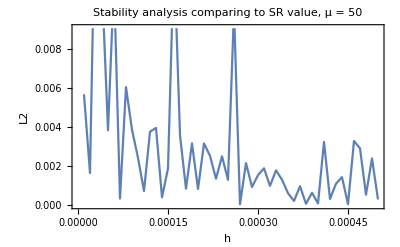

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9724469768090942)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{60,0.97433,0.0478578}

```mathematica
ld ={{0.00001,0.9667666899905327},{0.00002,0.9740975700661947},{0.000030000000000000004,0.9546738720791738},{0.00004,0.9611231627822723},{0.00005,0.9762819674492542},{0.00006,0.9839014884293957},{0.00007000000000000001,0.9727847971791552},{0.00008,0.9784946028501912},{0.00009,0.9763140071491669},{0.0001,0.974872148101264},{0.00011,0.973170327510521},{0.00012,0.9686860053379456},{0.00013000000000000002,0.968489435089914},{0.00014000000000000001,0.9728506122411247},{0.00015000000000000001,0.9743304271498294},{0.00016,0.9853475201772545},{0.00017,0.9760309829043106},{0.00018,0.973292984623259},{0.00019,0.9756112725665292},{0.0002,0.9716186816918531},{0.00021,0.9692841778083892},{0.00022,0.9699191998308445},{0.00023,0.9710940511669666},{0.00024,0.9699442453038717},{0.00025,0.9711477496973174},{0.00026000000000000003,0.9824169334317739},{0.00027000000000000006,0.9724001683023802},{0.0002800000000000001,0.9702916535499201},{0.00029000000000000006,0.9715146574578735},{0.00030000000000000003,0.9709086053095219},{0.00031000000000000005,0.9705588174093362},{0.00032,0.9734346335849269},{0.00033000000000000005,0.9706631295167588},{0.0003400000000000001,0.9711420611911445},{0.00035000000000000005,0.9718340627591324},{0.0003600000000000001,0.9726623434331472},{0.0003700000000000001,0.9734173671373225},{0.0003800000000000001,0.972518407154198},{0.00039000000000000005,0.9730830690695095},{0.0004000000000000001,0.972534884796107},{0.00041000000000000005,0.969210293739366},{0.00042000000000000007,0.9721283812515351},{0.0004300000000000001,0.9713476248500381},{0.00044000000000000007,0.9710117531734839},{0.00045000000000000004,0.9723944790023777},{0.00046000000000000007,0.9691592255002546},{0.00047000000000000004,0.9753581130526887},{0.00048000000000000007,0.9729837125402084},{0.0004900000000000001,0.9748376457791601},{0.0005000000000000001,0.9721565566632839}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.972402

0.00471871

```mathematica
0.03885616951315774
```

### μ = 70

```mathematica
p= 4;
μ=70;
M :=0.007904557686466
ϕini =59.87862053819866;
ϕend=69.30346456329042;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.1 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.1 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3.09 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.08316×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.882523},{0.00002,0.95745},{0.00003,0.988844},{0.00004,0.986661},{0.00005,0.989937},{0.00006,0.96487},{0.00007,0.961277},{0.00008,0.970438},{0.00009,0.968753},{0.0001,0.977449},{0.00011,0.980384},{0.00012,0.976173},{0.00013,0.976862},{0.00014,0.972841},{0.00015,0.972948},{0.00016,0.967826},{0.00017,0.972453},{0.00018,0.965791},{0.00019,0.975197},{0.0002,0.97158},{0.00021,0.972198},{0.00022,0.97507},{0.00023,0.980183},{0.00024,0.974522},{0.00025,0.973121},{0.00026,0.975047},{0.00027,0.971053},{0.00028,0.969978},{0.00029,0.970439},{0.0003,0.972333},{0.00031,0.974558},{0.00032,0.973784},{0.00033,0.977503},{0.00034,0.9775},{0.00035,0.973178},{0.00036,0.971855},{0.00037,0.969541},{0.00038,0.9707},{0.00039,0.971148},{0.0004,0.972454},{0.00041,0.975225},{0.00042,0.972274},{0.00043,0.974493},{0.00044,0.973278},{0.00045,0.975237},{0.00046,0.96903},{0.00047,0.972085},{0.00048,0.970985},{0.00049,0.971233},{0.0005,0.971296}}

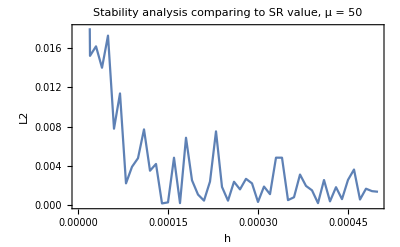

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9726620671429493)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{70,0.972948,0.0506881}

```mathematica
ld ={{0.00006,0.9648702769519545},{0.00007000000000000001,0.9612771634199166},{0.00008,0.970437726420816},{0.00009,0.9687532805568924},{0.0001,0.9774494622435244},{0.00011,0.9803835518302415},{0.00012,0.9761730308084765},{0.00013000000000000002,0.9768620897822521},{0.00014000000000000001,0.9728405590332255},{0.00015000000000000001,0.9729483822566105},{0.00016,0.9678260626012782},{0.00017,0.9724527875307274},{0.00018,0.9657911333761017},{0.00019,0.9751965293078722},{0.0002,0.9715804575678014},{0.00021,0.9721981922264149},{0.00022,0.9750700510603543},{0.00023,0.9801826279623795},{0.00024,0.974521939683444},{0.00025,0.9731209098534801},{0.00026000000000000003,0.975047012804151},{0.00027000000000000006,0.9710526356164907},{0.0002800000000000001,0.9699780843011968},{0.00029000000000000006,0.9704391893268308},{0.00030000000000000003,0.9723326269538075},{0.00031000000000000005,0.9745579580104391},{0.00032,0.973783570668253},{0.00033000000000000005,0.9775025799910703},{0.0003400000000000001,0.9774998814437537},{0.00035000000000000005,0.9731782993881799},{0.0003600000000000001,0.9718546511667682},{0.0003700000000000001,0.9695412188362953},{0.0003800000000000001,0.9707003605487214},{0.00039000000000000005,0.9711482438581},{0.0004000000000000001,0.972454174752632},{0.00041000000000000005,0.9752253420771181},{0.00042000000000000007,0.9722735942521953},{0.0004300000000000001,0.9744932479322749},{0.00044000000000000007,0.9732778606105504},{0.00045000000000000004,0.9752365000816486},{0.00046000000000000007,0.9690295897986414},{0.00047000000000000004,0.972084949892871},{0.00048000000000000007,0.970984746870644},{0.0004900000000000001,0.9712326798709955},{0.0005000000000000001,0.9712956271021532}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.972581

0.00367346

```mathematica
0.03885616951315774
```

### μ = 80

```mathematica
p= 4;
μ=80;
M :=0.008186832746510116
ϕini =69.77270710592848;
ϕend=79.30215864872666;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.05 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.05 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3. 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.03745×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.968531},{0.00002,0.984458},{0.00003,0.928678},{0.00004,0.946943},{0.00005,0.964413},{0.00006,0.975415},{0.00007,0.976796},{0.00008,0.974747},{0.00009,0.978158},{0.0001,0.972885},{0.00011,0.952111},{0.00012,0.972797},{0.00013,0.975748},{0.00014,0.968479},{0.00015,0.97188},{0.00016,0.974158},{0.00017,0.975024},{0.00018,0.975879},{0.00019,0.97386},{0.0002,0.971336},{0.00021,0.971452},{0.00022,0.970399},{0.00023,0.977338},{0.00024,0.970603},{0.00025,0.972904},{0.00026,0.97447},{0.00027,0.973849},{0.00028,0.973091},{0.00029,0.974643},{0.0003,0.975837},{0.00031,0.97168},{0.00032,0.971701},{0.00033,0.979746},{0.00034,0.971138},{0.00035,0.971214},{0.00036,0.971283},{0.00037,0.970621},{0.00038,0.972312},{0.00039,0.973968},{0.0004,0.973522},{0.00041,0.972988},{0.00042,0.974837},{0.00043,0.973343},{0.00044,0.974624},{0.00045,0.970783},{0.00046,0.971233},{0.00047,0.972048},{0.00048,0.973661},{0.00049,0.974135},{0.0005,0.972862}}

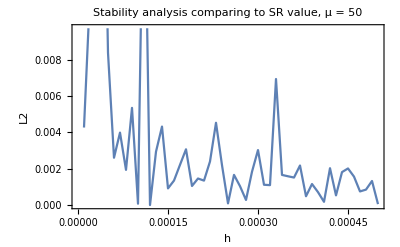

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9728037732025318)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{80,0.97188,0.0528901}

```mathematica
ld ={{0.00005,0.9644132712189921},{0.00006,0.9754154009152087},{0.00007000000000000001,0.9767957228865018},{0.00008,0.9747467507096645},{0.00009,0.9781584795978413},{0.0001,0.972885349671677},{0.00011,0.9521111464897274},{0.00012,0.9727973071908264},{0.00013000000000000002,0.975748048993563},{0.00014000000000000001,0.9684785851810414},{0.00015000000000000001,0.9718804192384515},{0.00016,0.9741579649591104},{0.00017,0.9750238378557977},{0.00018,0.9758789732776109},{0.00019,0.9738599869223913},{0.0002,0.971336223856933},{0.00021,0.9714519752040383},{0.00022,0.9703992767654741},{0.00023,0.9773380188764825},{0.00024,0.9706028400671717},{0.00025,0.9729035362066718},{0.00026000000000000003,0.9744703398248034},{0.00027000000000000006,0.9738494360115246},{0.0002800000000000001,0.9730912775608404},{0.00029000000000000006,0.9746432025081352},{0.00030000000000000003,0.9758372212546264},{0.00031000000000000005,0.97168042509571},{0.00032,0.9717009057660534},{0.00033000000000000005,0.9797457347121306},{0.0003400000000000001,0.9711382891641029},{0.00035000000000000005,0.9712135300933163},{0.0003600000000000001,0.9712832057790877},{0.0003700000000000001,0.970620903205769},{0.0003800000000000001,0.9723124247297406},{0.00039000000000000005,0.9739682883306694},{0.0004000000000000001,0.973521697133071},{0.00041000000000000005,0.9729884666395148},{0.00042000000000000007,0.9748370729056346},{0.0004300000000000001,0.9733428664501478},{0.00044000000000000007,0.9746235573523292},{0.00045000000000000004,0.9707830333611397},{0.00046000000000000007,0.9712326002203111},{0.00047000000000000004,0.9720476373947793},{0.00048000000000000007,0.9736606971380064},{0.0004900000000000001,0.9741347079327207},{0.0005000000000000001,0.972862399140062}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.972739

0.00403717

```mathematica
0.03885616951315774
```

### μ = 90

```mathematica
p= 4;
μ=90;
M :=0.008441292799808561
ϕini =79.69003470391434;
ϕend=89.30113989791752;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.01 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  3.01 10^6}, MaxStepSize->500,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      3. 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

3.00318×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.934074},{0.00002,0.93694},{0.00003,0.970834},{0.00004,0.965315},{0.00005,0.970681},{0.00006,0.974405},{0.00007,0.970519},{0.00008,0.976203},{0.00009,0.970676},{0.0001,0.975691},{0.00011,0.971415},{0.00012,0.972723},{0.00013,0.978328},{0.00014,0.973087},{0.00015,0.971481},{0.00016,0.972099},{0.00017,0.974303},{0.00018,0.973363},{0.00019,0.973364},{0.0002,0.971077},{0.00021,0.971567},{0.00022,0.972668},{0.00023,0.970751},{0.00024,0.972031},{0.00025,0.97088},{0.00026,0.973044},{0.00027,0.974632},{0.00028,0.974498},{0.00029,0.97403},{0.0003,0.974543},{0.00031,0.972373},{0.00032,0.971861},{0.00033,0.972598},{0.00034,0.971885},{0.00035,0.974928},{0.00036,0.97313},{0.00037,0.973076},{0.00038,0.972177},{0.00039,0.972983},{0.0004,0.972539},{0.00041,0.972521},{0.00042,0.973125},{0.00043,0.97227},{0.00044,0.972013},{0.00045,0.972654},{0.00046,0.972249},{0.00047,0.973277},{0.00048,0.973211},{0.00049,0.972018},{0.0005,0.971439}}

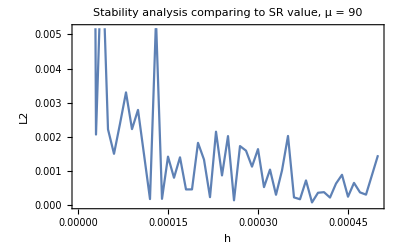

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.972901953693959)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 90 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{90,0.971481,0.054656}

```mathematica
ld ={{0.00005,0.9706814455034845},{0.00006,0.9744051227825052},{0.00007000000000000001,0.9705187842433924},{0.00008,0.9762031422930243},{0.00009,0.97067562640717},{0.0001,0.9756906649693059},{0.00011,0.9714153546866164},{0.00012,0.9727230159020646},{0.00013000000000000002,0.9783283979128201},{0.00014000000000000001,0.9730872737338551},{0.00015000000000000001,0.9714814859179264},{0.00016,0.9720990060468885},{0.00017,0.9743029053127952},{0.00018,0.9733629614265282},{0.00019,0.9733640536275479},{0.0002,0.9710770602198351},{0.00021,0.9715672721244148},{0.00022,0.9726675111754529},{0.00023,0.9707508946496132},{0.00024,0.9720306160672396},{0.00025,0.9708797822505848},{0.00026000000000000003,0.9730442318021904},{0.00027000000000000006,0.9746320466068569},{0.0002800000000000001,0.9744976168721778},{0.00029000000000000006,0.9740302314621947},{0.00030000000000000003,0.9745431049071627},{0.00031000000000000005,0.9723733627689811},{0.00032,0.9718605914753634},{0.00033000000000000005,0.9725976559016927},{0.0003400000000000001,0.9718853989594511},{0.00035000000000000005,0.9749280647815245},{0.0003600000000000001,0.9731300358570663},{0.0003700000000000001,0.9730756180061267},{0.0003800000000000001,0.9721773988059346},{0.00039000000000000005,0.972982526446464},{0.0004000000000000001,0.9725385336978004},{0.00041000000000000005,0.9725209578649242},{0.00042000000000000007,0.9731250128002911},{0.0004300000000000001,0.9722701394572263},{0.00044000000000000007,0.9720127856078759},{0.00045000000000000004,0.9726541370951685},{0.00046000000000000007,0.9722493950974996},{0.00047000000000000004,0.9732766214025848},{0.00048000000000000007,0.9732105864722852},{0.0004900000000000001,0.9720180673960711},{0.0005000000000000001,0.9714391772183192}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.972834

0.00156064

```mathematica
0.03885616951315774
```

### μ = 100

```mathematica
p= 4;
μ=100;
M :=0.008673753138812312
ϕini =89.623730539419;
ϕend=99.30032297682622;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,2.99 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,  2.99 10^6}, MaxStepSize->1000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision, WorkingPrecision->MachinePrecision,PrecisionGoal->Automatic];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,      2.97 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

```mathematica
tend
```

2.97657×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, StartingStepSize->.0001,MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.0001,AccuracyGoal->MachinePrecision,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+ k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

```mathematica
r[0.002]
```

0.0561132

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.0005, 0.00001}]]
```

{{0.00001,0.999705},{0.00002,0.995161},{0.00003,0.988696},{0.00004,0.981642},{0.00005,0.975146},{0.00006,0.970184},{0.00007,0.967518},{0.00008,0.967121},{0.00009,0.968626},{0.0001,0.971153},{0.00011,0.973884},{0.00012,0.975871},{0.00013,0.97677},{0.00014,0.976365},{0.00015,0.975003},{0.00016,0.973229},{0.00017,0.971582},{0.00018,0.970592},{0.00019,0.970498},{0.0002,0.971237},{0.00021,0.972487},{0.00022,0.973824},{0.00023,0.974823},{0.00024,0.975157},{0.00025,0.974773},{0.00026,0.973838},{0.00027,0.972711},{0.00028,0.971727},{0.00029,0.971227},{0.0003,0.971322},{0.00031,0.971923},{0.00032,0.97285},{0.00033,0.973752},{0.00034,0.974336},{0.00035,0.974413},{0.00036,0.973976},{0.00037,0.973187},{0.00038,0.972314},{0.00039,0.971641},{0.0004,0.971376},{0.00041,0.971601},{0.00042,0.972201},{0.00043,0.972958},{0.00044,0.973619},{0.00045,0.973961},{0.00046,0.973854},{0.00047,0.973358},{0.00048,0.972627},{0.00049,0.971908},{0.0005,0.971434}}

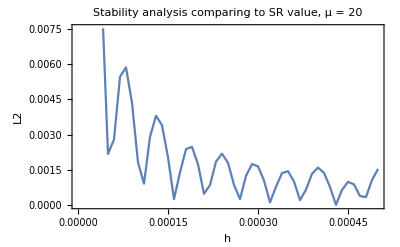

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.97297186245833)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 20 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
ld = {{0.000030000000000000004,0.9886955576422599},{0.00004,0.9816424358109809},{0.00005,0.975146335177676},{0.00006,0.9701838450417904},{0.00007000000000000001,0.9675179924878508},{0.00008,0.9671210972556076},{0.00009,0.9686261151461405},{0.0001,0.9711526094748703},{0.00011,0.973884137736697},{0.00012,0.9758714168412237},{0.00013000000000000002,0.9767695896835787},{0.00014000000000000001,0.9763649207842842},{0.00015000000000000001,0.9750034082406239},{0.00016,0.97322858182097},{0.00017,0.9715816169239887},{0.00018,0.9705924451871111},{0.00019,0.9704976236112108},{0.0002,0.9712369394930407},{0.00021,0.9724874946157396},{0.00022,0.9738240986059973},{0.00023,0.9748234592957261},{0.00024,0.9751569528412387},{0.00025,0.9747725366634881},{0.00026000000000000003,0.9738376089940973},{0.00027000000000000006,0.9727112798590418},{0.0002800000000000001,0.9717273028114127},{0.00029000000000000006,0.9712265745491726},{0.00030000000000000003,0.9713221285985023},{0.00031000000000000005,0.9719227582728727},{0.00032,0.9728503241928232},{0.00033000000000000005,0.9737519217022325},{0.0003400000000000001,0.9743362494219475},{0.00035000000000000005,0.9744132656737271},{0.0003600000000000001,0.973975631273291},{0.0003700000000000001,0.9731871775699642},{0.0003800000000000001,0.9723138964652097},{0.00039000000000000005,0.9716413806577734},{0.0004000000000000001,0.9713755833673156},{0.00041000000000000005,0.9716007864544107},{0.00042000000000000007,0.972201251786231},{0.0004300000000000001,0.9729581963704009},{0.00044000000000000007,0.9736185121887917},{0.00045000000000000004,0.9739614383382195},{0.00046000000000000007,0.9738542928278497},{0.00047000000000000004,0.9733575811840935},{0.00048000000000000007,0.9726267785163962},{0.0004900000000000001,0.9719075270396359},{0.0005000000000000001,0.9714335234836218}};
Mean[ld[[;;,2]]]
StandardDeviation[ld[[;;,2]]]
```

0.973214

0.0033095

### Analysis of derivative

```mathematica
nsder4 = {{0.00001,1.0517992076452476},{0.00002,1.0146226260582258},{0.000030000000000000004,0.9655108370949831},{0.00004,0.9680369507929264},{0.00005,0.976429921117339},{0.00006,0.9820053280439776},{0.00007000000000000001,0.9603482076899903},{0.00008,0.9626999835898907},{0.00009,0.9634852342842778},{0.0001,0.9687332701123703},{0.00011,0.9815301340610119},{0.00012,0.9777903280672392},{0.00013000000000000002,0.973333797312476},{0.00014000000000000001,0.9759573850236737},{0.00015000000000000001,0.9690771336503062},{0.00016,0.9740548678169789},{0.00017,0.97091465234847},{0.00018,0.9718053734673429},{0.00019,0.970672170172415},{0.0002,0.9686636657570217},{0.00021,0.9697389693483419},{0.00022,0.9738317274056616},{0.00023,0.9740130607109984},{0.00024,0.974783804903958},{0.00025000000000000006,0.9732398501141911},{0.0002600000000000001,0.9773699343371318},{0.00027000000000000006,0.9750954381192107},{0.0002800000000000001,0.9703665820873946},{0.00029000000000000006,0.9726575433578044},{0.0003000000000000001,0.9742831731458373},{0.00031000000000000005,0.9716271339792693},{0.0003200000000000001,0.9714877316560425},{0.00033000000000000005,0.972967177810997},{0.0003400000000000001,0.9768219601295572},{0.00035000000000000005,0.9734907499094667},{0.0003600000000000001,0.9755377242378559},{0.00037000000000000005,0.9714859535740638},{0.0003800000000000001,0.9726000231297067},{0.00039000000000000005,0.9692611291616459},{0.0004000000000000001,0.9709123682765453},{0.00041000000000000005,0.9723161596315013},{0.00042000000000000007,0.9728404247755904},{0.00043000000000000004,0.974426456095984},{0.00044000000000000007,0.9764812686663459},{0.00045000000000000004,0.9747999628952512},{0.00046000000000000007,0.9733773927384173},{0.00047000000000000004,0.9747365869709215},{0.00048000000000000007,0.9723609192138875},{0.0004900000000000001,0.9728800211084885},{0.0005000000000000001,0.9723341587044668},{0.0005100000000000001,0.9734888622769576},{0.0005200000000000001,0.9708898698615305},{0.0005300000000000001,0.9727968301390554},{0.0005400000000000001,0.9732533380723585},{0.0005500000000000001,0.9748422830322531},{0.0005600000000000001,0.9754905936213842},{0.0005700000000000001,0.9751663813111598},{0.0005800000000000001,0.9731454737770904},{0.0005900000000000001,0.9716571164745617},{0.0006000000000000001,0.9725188051007176},{0.0006100000000000001,0.9711623010102752},{0.0006200000000000001,0.9725843309177263},{0.0006300000000000001,0.9728041007412771},{0.00064,0.9731875484605469},{0.0006500000000000001,0.9734963122734807},{0.0006600000000000001,0.9755290352631955},{0.0006700000000000001,0.9747021080907461},{0.00068,0.9741336683906889},{0.0006900000000000001,0.9740011714853816},{0.0007000000000000001,0.971543168469192},{0.0007100000000000001,0.9738915052768391},{0.00072,0.971881808493576},{0.0007300000000000001,0.9720711598267276},{0.0007400000000000001,0.9722526661598972},{0.0007500000000000001,0.9741908472580819},{0.00076,0.9761840360211331},{0.0007700000000000001,0.976442170038729},{0.0007800000000000001,0.9747218870735939},{0.0007900000000000001,0.9741503601590983},{0.0008,0.9739837038589625},{0.0008100000000000001,0.9738608243806769},{0.0008200000000000001,0.9744362439074126},{0.0008300000000000001,0.9728166556175588},{0.00084,0.9722978934740725},{0.0008500000000000001,0.9755284967170988},{0.0008600000000000001,0.978020647769353},{0.0008700000000000001,0.9790594388404013},{0.00088,0.9753880273690809},{0.0008900000000000001,0.973955928613392},{0.0009000000000000001,0.9763075549121937},{0.0009100000000000001,0.9802642831831822},{0.00092,0.978342383700585},{0.00093,0.9710880954553924},{0.0009400000000000001,0.9690747366505883},{0.0009500000000000001,0.9857164325090855},{0.00096,1.0065068760293159},{0.0009700000000000002,0.9997222831482251},{0.0009800000000000002,0.951439659176041}};
```

```mathematica
Mean[Transpose[nsder4][[2]]]
StandardDeviation[Transpose[nsder4][[2]]]
```

0.974955

0.0107004

```mathematica
nsder2= {{0.00001,0.9922022722179367},{0.00002,0.9957785367831472},{0.000030000000000000004,0.9902464196779293},{0.00004,0.9807887768057183},{0.00005,0.9752363666972738},{0.00006,0.9696934197730607},{0.00007000000000000001,0.9680763320094804},{0.00008,0.9682802913760469},{0.00009,0.968193848191502},{0.0001,0.9706508200144819},{0.00011,0.9741429343127769},{0.00012,0.9761837188907001},{0.00013000000000000002,0.9769440315832264},{0.00014000000000000001,0.9764369618382113},{0.00015000000000000001,0.9747984559575344},{0.00016,0.9732377799377048},{0.00017,0.9722609162185394},{0.00018,0.9703167650767399},{0.00019,0.9700604141510663},{0.0002,0.970925904278762},{0.00021,0.9727865892297223},{0.00022,0.9738695729965836},{0.00023,0.9746947103056949},{0.00024,0.9750526343149222},{0.00025000000000000006,0.9747657885120707},{0.0002600000000000001,0.9737496892520616},{0.00027000000000000006,0.9724266439019806},{0.0002800000000000001,0.9719926891014959},{0.00029000000000000006,0.9712943490324312},{0.0003000000000000001,0.9715305604362231},{0.00031000000000000005,0.9717014597646129},{0.0003200000000000001,0.9732504395970986},{0.00033000000000000005,0.9736010830187607},{0.0003400000000000001,0.9744077654671414},{0.00035000000000000005,0.9741992615166084},{0.0003600000000000001,0.9738694044814475},{0.00037000000000000005,0.9729987504052281},{0.0003800000000000001,0.9722851292849468},{0.00039000000000000005,0.9716778901402978},{0.0004000000000000001,0.9711624248228399},{0.00041000000000000005,0.9714475008728939},{0.00042000000000000007,0.9723495574722906},{0.00043000000000000004,0.9730552703163347},{0.00044000000000000007,0.9737893326438537},{0.00045000000000000004,0.9739449452073219},{0.00046000000000000007,0.9736527898870853},{0.00047000000000000004,0.9733672959523466},{0.00048000000000000007,0.9726964827290112},{0.0004900000000000001,0.9717302146298797},{0.0005000000000000001,0.9714227664199876},{0.0005100000000000001,0.9712786243854502},{0.0005200000000000001,0.971507630106044},{0.0005300000000000001,0.9725314923546863},{0.0005400000000000001,0.9730127349760879},{0.0005500000000000001,0.9736017111027262},{0.0005600000000000001,0.9734263655162705},{0.0005700000000000001,0.9733896581208697},{0.0005800000000000001,0.9728761744553247},{0.0005900000000000001,0.9720181232007765},{0.0006000000000000001,0.9715931977415914},{0.0006100000000000001,0.9711102491322681},{0.0006200000000000001,0.9713195510735169},{0.0006300000000000001,0.9717189313403821},{0.00064,0.9722258742426878},{0.0006500000000000001,0.9728911583557365},{0.0006600000000000001,0.9733134572078828},{0.0006700000000000001,0.9731569265642125},{0.00068,0.9727442406947393},{0.0006900000000000001,0.9721514888732669},{0.0007000000000000001,0.9714131666717409},{0.0007100000000000001,0.970873897567946},{0.00072,0.9710596381812318},{0.0007300000000000001,0.9709959337936206},{0.0007400000000000001,0.9716494101060917},{0.0007500000000000001,0.9721938648654485},{0.00076,0.9727370243331278},{0.0007700000000000001,0.9728151494520345},{0.0007800000000000001,0.9725415681501477},{0.0007900000000000001,0.9720317367813205},{0.0008,0.9714549467816002},{0.0008100000000000001,0.970740279303591},{0.0008200000000000001,0.9703648522440061},{0.0008300000000000001,0.9705606651872578},{0.00084,0.9709720606682908},{0.0008500000000000001,0.9715574319668798},{0.0008600000000000001,0.9719204932923009},{0.0008700000000000001,0.9722237234089779},{0.00088,0.9721885029859025},{0.0008900000000000001,0.9718669591285305},{0.0009000000000000001,0.9710082174723279},{0.0009100000000000001,0.9704745723775899},{0.00092,0.9699727255345976},{0.00093,0.9698064201728968},{0.0009400000000000001,0.9701162783172687},{0.0009500000000000001,0.9707290472378156},{0.00096,0.9714320437544519},{0.0009700000000000002,0.9717593454000191},{0.0009800000000000002,0.9716939031074457},{0.0009900000000000002,0.9713924593360944},{0.0010000000000000002,0.970667257862113}};
```

```mathematica
Mean[Transpose[nsder2][[2]]]
StandardDeviation[Transpose[nsder2][[2]]]
```

0.972903

0.00397211

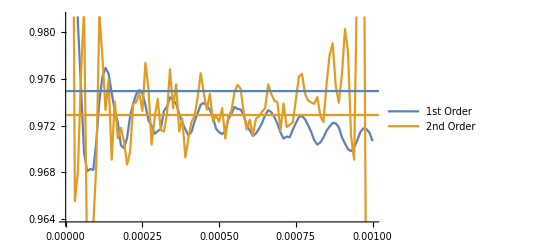

```mathematica
Show[ListPlot[{nsder2,nsder4}//Evaluate,Joined->True,PlotLegends->{"1st Order", "2nd Order"}] ,Plot[{0.9749549629050269,0.9729030912239217 }, {t,0,100}]]
```

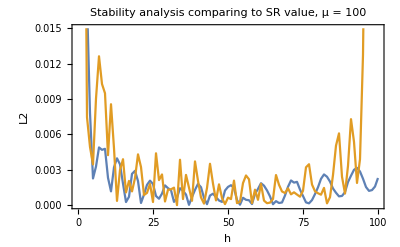

```mathematica
erro1 = Sqrt[(Transpose[nsder2][[2]] -0.97297186245833)^2];
erro2= Sqrt[(Transpose[nsder4][[2]] -0.97297186245833)^2];
Show[ListPlot[{erro1,erro2}//Evaluate,Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 100 ", Frame->True, FrameLabel->{"h","L2"},PlotRange->{0,0.015}]]
```

```mathematica
PS[0.05]
```

2.16961×10^-9

```mathematica
h2 = 0.00015;
{μ, nS[0.002],r[0.002]}
```

{20,0.967768,0.0199592}

## Plotting

```mathematica
res = {{1,0.9420736577632982,1.7774602771495019*^-6},
{2,0.9429943965017721,0.000025231684736272145},
{3,0.945783421995048,0.00011464787325682974},
{4,0.9471891676435628,0.00032290771704225645},
{5,0.9473717635101696,0.0006947257707137265},
{6,0.9519568938823263,0.0012605937875081303},
{7,0.9543732058140167,0.002026653030120331},
{8,0.9549988959094287,0.0029827211689610004},
{9,0.9560938816464495,0.004106889178494394},
{10,0.9590680463234112,0.005367297367410439},
{11,0.9598617874564745,0.006732378459605959},
{12,0.9612106127037979,0.008178534391129985},
{13,0.9622909730517709,0.009667512062095762},
{14,0.9624180438009775,0.011185901084695044},
{15,0.9634523473550928,0.012707849639121256},
{16,0.965487327386421,0.014215355174508722},
{17,0.965556215093907,0.01570464337151316},
{18,0.9664866711585253,0.017163374827844018},
{19,0.9669989375304979,0.01857880582282477},
{20,0.9675272548820055,0.01995073934909523}

};
```

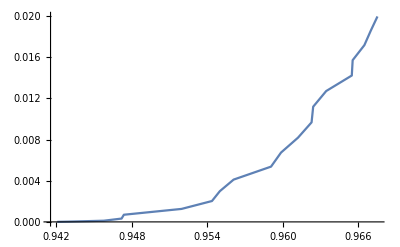

```mathematica
ListLinePlot[res[[;;,2;;3]]]
```

## Plotting Mean values of nS along h2 N = 60

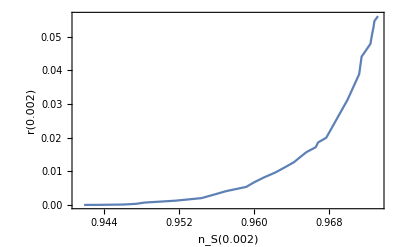

```mathematica
res = {{1,0.9418284158630357, 1.7774602771495019*^-6},
{2,0.9433648948278768, 0.000025231684736272145},
{3,0.9459646017967449, 0.00011464787325682974},
{4, 0.9473632971084776, 0.00032290771704225645},
{5,0.94824895288486, 0.0006947257707137265},
{6,0.9515601407481834, 0.0012605937875081303 },
{7,0.9543661858921217,0.002026653030120331},
{8, 0.9555902910692069, 0.0029827211689610004},
{9,0.9570063358927433,  0.004106889178494394},
{10, 0.9591493772050897, 0.005367297367410439},
{11, 0.9599881966998464,0.006732378459605959 },
{12,0.9610373895659212, 0.008178534391129985},
{13,0.9622706913576015, 0.009667512062095762},
{14, 0.9632695258005722, 0.011185901084695044},
{15, 0.9642431164964678, 0.012707849639121256},
{16,0.9649018899082524, 0.014215355174508722},
{17,0.9655766621823028, 0.01570464337151316},
{18,0.9665678204211184,0.017163374827844018},
{19,0.9668154054082477,  0.01857880582282477},
{20,0.9676855475136105,0.019959206101410453},
{30,0.9699608502011791, 0.031247530640802938},
{40,0.971202012632072, 0.03885616951315774},
{50,0.9714639023016218,0.04406669485057957 },
{60,0.9724019311766396, 0.04785775778625682},
{70,0.9725809075695456, 0.0506881424427939},
{80,0.9727385442562914,0.05289012068381991},
{90,0.9728344712177455, 0.054655968435726225},
{100,0.9732144621246067,0.05611318204090545 }
};

plot1 =ListPlot[res[[;;,2;;3]], Joined->True,Frame->True,FrameLabel->{"n_S(0.002)", "r(0.002)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\k0002_n60_mean_h2.csv",res];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\ns_vs.r0002_meanh2.png",plot1];
```

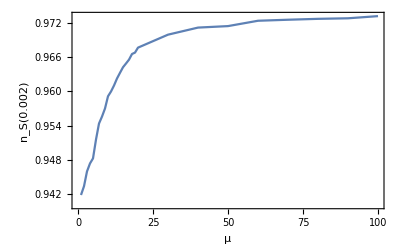

```mathematica
plot2=ListPlot[res[[;;,1;;2]],Joined->True,Frame->True, FrameLabel->{"μ","n_S(0.002)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\mu_vs.ns0002_meanh2.png",plot2];
```

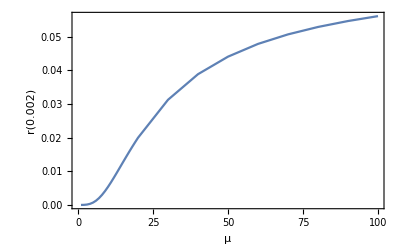

```mathematica
plot3=ListPlot[Table[{res[[μ,1]], res[[μ,3]]},{μ,Length[res]}],Joined->True,Frame->True, FrameLabel->{"μ","r(0.002)"}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\mu_vs.r0002_meanh2.png",plot3];
```